# Tuning the SOC gap and M point higher order Van Hove singularities in the surface bands of Sr_2 RuO_4

Anirudh Chandrasekaran

Loughborough University
11 June 2024

## Loading the Library

We first load the library by executing the following:

```mathematica
AppendTo[$Path,StringDelete[NotebookDirectory[],"/Sr2RuO4"]<>"Package"];
<<BandUtilities`
```

## Outline of the strategy

We will begin by loading and interpolating the tight-binding models for various values of θ and then separately load and interpolate through the models with nematic term added. We will then interpolate linearly between the nematicity free model and the model with the nematic term to generate a continuously tunable model.

## Interpolating between the Wannier90 files

### Ingredients needed for symmetrization

```mathematica
ρ={{0,-1,0},{1,0,0},{0,0,1}}; (*The matrix part of the Subscript[C, 4] rotation about one of the Ru atoms.*)
Uρ={{0,-1,0},{1,0,0},{0,0,-1}}; (*Representation of Subscript[C, 4] rotation in the d-orbital space.*)

rxy={{0,1,0},{1,0,0},{0,0,1}};  (*x<->y reflection.*)
Urxy={{-1,0,0},{0,1,0},{0,0,-1}}; (*Representation of the x<->y reflection.*)

c0={1/4,3/4,0}; (*Location of one of the Ru atoms, which we shall use as the centre of the Subscript[C, 4] rotation.*)

AtomLocations={{3/4,1/4,0},{3/4,1/4,0},{3/4,1/4,0},{1/4,3/4,0},{1/4,3/4,0},{1/4,3/4,0}}; (*Location of the basis atoms in the fractional coordinates within the unit cell.*)

SymmetryList={}; (*This is a multidimensional list which we shall construct below. Each element is a sublist corresponding to a particular symmetry. First element of the sublist is real space symmetry's matrix part, second element is the translation part and the third element is its representation in the Hilbert space. Our point group is Subscript[D, 4], or Subscript[D, 8] in some pepole's notation.*)
Do[
AppendTo[SymmetryList,{MatrixPower[ρ,i],(c0-MatrixPower[ρ,i].c0)//Simplify,ArrayFlatten[IdentityMatrix[2]⊗MatrixPower[Uρ,i]]}];

AppendTo[SymmetryList,{MatrixPower[ρ,i].rxy,(c0-MatrixPower[ρ,i].c0)//Simplify,ArrayFlatten[IdentityMatrix[2]⊗MatrixPower[Uρ,i]].ArrayFlatten[{{0,1},{1,0}}⊗Urxy]}];
,{i,1,4}];
```

### Interpolation with symmetrization

We now interpolate between the Wannier90 data for 13 different rotations of the RuO octahedra: 0° through 12° to generate a continuously θ dependent Hamiltonian, whilst ensuring that the interpolated model has the right symmetry (for which we are feeding the list SymmetryList):

```mathematica
FileLocn=NotebookDirectory[]<>"unrenormalized2/";

W90Data=LoadInterpolateTBMs[{FileLocn<>"Sr2RuO4_0deg.dat",FileLocn<>"Sr2RuO4_1deg.dat",FileLocn<>"Sr2RuO4_2deg.dat",FileLocn<>"Sr2RuO4_3deg.dat",FileLocn<>"Sr2RuO4_4deg.dat",FileLocn<>"Sr2RuO4_5deg.dat",FileLocn<>"Sr2RuO4_6deg.dat",FileLocn<>"Sr2RuO4_7deg.dat",FileLocn<>"Sr2RuO4_8deg.dat",FileLocn<>"Sr2RuO4_9deg.dat",FileLocn<>"Sr2RuO4_10deg.dat",FileLocn<>"Sr2RuO4_11deg.dat",FileLocn<>"Sr2RuO4_12deg.dat"},{0,1,2,3,4,5,6,7,8,9,10,11,12},"Symmetries"->SymmetryList,"OrbitalCentres"->AtomLocations,"ParameterSymbol"->"θ"];

Hamltn1[k1_,k2_,θ_]=W90Data[[1]];
```

Invalid or no lattice vectors provided! Using unit vectors.

Tight-binding data files loaded.

Space dimension: 3

Number of orbitals: 6

Number of supercells: 49

Number of models/data-files to interpolate: 13

Number of lines in the data files: {741,853,853,853,845,853,853,853,853,853,853,853,853}

Interpolating between the Hamiltonians.

Valid symmetrization scheme provided! We will symmetrize the loaded Hamiltonian.

Number of supercells after symmetrization: 79

## Phenomenological spin orbit term

We now construct the phenomenological SOC terms:

```mathematica
Lx={{0,0,ⅈ},{0,0,0},{-ⅈ,0,0}};
Ly={{0,0,0},{0,0,ⅈ},{0,-ⅈ,0}};
Lz={{0,-ⅈ,0},{ⅈ,0,0},{0,0,0}};

Hupup=1/2 Lz;
Hupdown=1/2(Lx+ⅈ Ly); 
Hdownup=1/2(Lx-ⅈ Ly);
Hdowndown=-1/2 Lz;
Zero2=ConstantArray[0,{3,3}];


HSOC=Join[Join[Hupup,Zero2,Hupdown,Zero2,2],Join[Zero2,Hupup,Zero2,Hupdown,2],Join[Hdownup,Zero2,Hdowndown,Zero2,2],Join[Zero2,Hdownup,Zero2,Hdowndown,2]];
```

## Reconstructing the full interpolated Hamiltonian

The full Hamiltonian incorporating SOC with tunable SOC strength and tunable θ. A version for the √2×√2 unit cell that is tailor made for fitting to the ARPES data is also defined (since the bulk has one Ru atom per unit cell, its Brillouin zone has twice the area of the default surface band BZ, which is also ‘rotated’ by 45°).

```mathematica
Hamiltonian1[k1_,k2_,θ_,λ_]=0.5(ArrayFlatten[IdentityMatrix[2]⊗Hamltn1[k1,k2,θ]]+λ HSOC+ComplexExpand[ConjugateTranspose[ArrayFlatten[IdentityMatrix[2]⊗Hamltn1[k1,k2,θ]]+λ HSOC]]);
```

We can check the eigenvalues at a high symmetry point to see if the symmetrisation was successful, and has eliminated the weak splitting of degeneracies at the high symmetry points

## Loading and interpolating the nematic models

```mathematica
FileLocn2=NotebookDirectory[]<>"renormalized/";

W90Data2=LoadInterpolateTBMs[{FileLocn2<>"Sr2RuO4_EXP_Monolayer_1theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_1theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_2theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_3theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_4theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_5theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_6theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_7theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_8theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_9theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_10theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_11theta_0phi1_0phi2_hr_sym_soc_nem.dat",FileLocn2<>"Sr2RuO4_EXP_Monolayer_12theta_0phi1_0phi2_hr_sym_soc_nem.dat"},{0,1,2,3,4,5,6,7,8,9,10,11,12},"ParameterSymbol"->"θ"];

Hamiltonian2[k1_,k2_,θ_]=W90Data2[[1]];
```

Invalid or no lattice vectors provided! Using unit vectors.

Tight-binding data files loaded.

Space dimension: 3

Number of orbitals: 12

Number of supercells: 49

Number of models/data-files to interpolate: 13

Number of lines in the data files: {1723,1723,1723,1723,1707,1723,1723,1723,1723,1723,1723,1723,1723}

Interpolating between the Hamiltonians.

No valid symmetrization scheme provided! We will not symmetrize the loaded Hamiltonian.

## Comparing the nematic and symmetric models

For the sake of plotting, let us define the Hamiltonians evaluated at θ=8° with and without the nematic term

```mathematica
HamTemp[k_]:=1000 0.2444Hamiltonian1[k[[1]]-k[[2]],k[[1]]+k[[2]],8,0.175]
HamTempNem[k_]:=1000Hamiltonian2[k[[1]]-k[[2]],k[[1]]+k[[2]],8]
```

Using these the bands can be generated

```mathematica
HSymmPts={{{0,π-3.869  0.36},"← Γ"},{{0,π},"M_y"},{{3.869 0.36,π},"X →"}};
Bnd1=GenerateBandStructure[HamTemp,HSymmPts];
Bnd2=GenerateBandStructure[HamTempNem,HSymmPts];
```

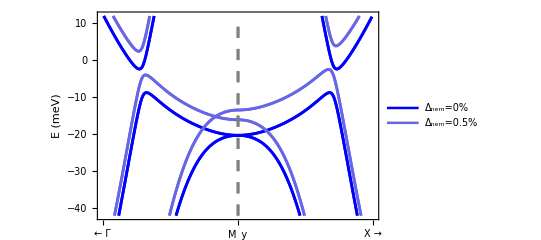

```mathematica
plt1=PlotBandStructure[Bnd1,{-42,12},"AspectRatio"->3/5,"yLabel"->{(*Label*)"E (meV)",(*Font Size*)12,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{12,Black,"Arial"},"yTicks"->{9,Black,"Arial"},"LineThickness"->0.005,"LineColorScheme"->{RGBColor[0,0,1]},"PlotKeyLegend"->{Style["Δ_nem=0%",FontSize->9,FontFamily->"Times"],Scaled[{0.51,1.01-1/17.}]}];

plt2=PlotBandStructure[Bnd2,{-42,12},"AspectRatio"->3/5,"yLabel"->{(*Label*)"E (meV)",(*Font Size*)12,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{12,Black,"Arial"},"yTicks"->{9,Black,"Arial"},"LineThickness"->0.005,"LineColorScheme"->{RGBColor[0.4,0.4,0.9]},"PlotKeyLegend"->{Style["Δ_nem=0.5%",FontSize->9,FontFamily->"Times"],Scaled[{0.51,1.01-2/17.}]}];

Show[plt1,plt2]
```

The degeneracy at the M_y point has been lifted which is to be expected since the nematic term breaks the r_xy reflection symmetry that causes the degeneracy.

## A continuously θ(°) and Δ_nem(%) tuned model

We will linearly interpolate between the nematicity free model and the nematic model for Δ_nem=0.5% (which corresponds to the QPI best fit). This can be obtained as follows:
H(k,Δ)=H_0(k)+Δ(H_0.5(k)-H_0(k))/(0.5-0)=(1-2Δ)H_0(k)+2Δ H_0.5(k).

```mathematica
HamiltonianNemTunedmeV[k1_,k2_,θ_,Δ_]=(1-2Δ)1000 0.2444Hamiltonian1[k1-k2,k1+k2,θ,0.175]+1000 2Δ Hamiltonian2[k1-k2,k1+k2,θ];

HamltnTuned[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],k[[3]],k[[4]]]

HamTempNem2[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],8,1(*Nematicity set to 1%*)]
```

#### Checking the interpolation

```mathematica
Bnd3=GenerateBandStructure[HamTempNem2,HSymmPts];
```

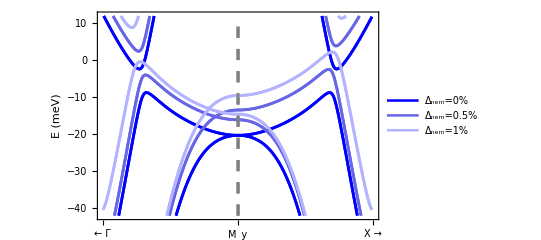

```mathematica
plt3=PlotBandStructure[Bnd3,{-42,12},"AspectRatio"->3/5,"yLabel"->{(*Label*)"E (meV)",(*Font Size*)12,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{12,Black,"Arial"},"yTicks"->{9,Black,"Arial"},"LineThickness"->0.005,"LineColorScheme"->{RGBColor[0.7,0.7,1]},"PlotKeyLegend"->{Style["Δ_nem=1%",FontSize->9,FontFamily->"Times"],Scaled[{0.51,1.01-3/17.}]}];

Show[plt1,plt2,plt3]
```

We can see that the interpolation scheme has worked.

### Iterating through Δ_nem and hunting for HOS

Let us outline the strategy that we shall adopt below. We iterate through a few values of Δ_nem including 0%, 0.5%, 1% and 2%. At each Δ_nem, we will try to tune the M point singularity and the SOC gap critical points to a HOS. We note down the θ_crit and the series expansion of the four bands.

Now the bands(points) of interest are 5&6 (M point), 7&8 (M point), 7&8 (SOC gap) and 9&10 (SOC gap). For 5&6 (M point) and 7&8 (M point), tuning to HOS is simpler. We are already at a critical point, namely the high symmetry M point. We compute det(Hes) as a function of δθ and set it to zero to solve for δθ. If we repeat this a few times we get θ_crit. But for the SOC gap critical points, we have to adopt a different strategy since the location of the critical point is not fixed and changes with θ and Δ_nem.

We will use a two-pronged strategy: first we choose a range of θ to investigate, say 8° to 10°. We locate the k_VHS for the angles at the end points of the range and compute the Hessian determinant. If they are of opposite sign, we expect the Hessian determinant to vanish somewhere in between. We will then use binary search to locate this θ_crit. We have to do this separately for both the bands, and on either sides of the SOC gap (which have been made inequivalent by the nematic term).

Firstly, we have to identify the range of k in which the SOC critical points seem to exist by plotting the dispersion for Δ_nem= 0%, 0.5%, 1% and 2% and θ=7°,8°,...,11°. This is needed since we need to identify a suitable range for the LocateCriticalPoint routine to work to find the actual k_VHS.

## Evolution of the band-structure

We plot a spaghetti plot showing the evolution of the band-structure with θ for different choices of Δ_nem (0%, 1% and 2%).

```mathematica
HSymmPtsNoLabel={{{0,π-3.869  0.35},""},{{0,π},""},{{3.869 0.35,π},""}};
AngleList={7,8,9,10,11};

OpacityList={0.1,0.2,0.35,0.5,1};
ColourChoice={67/255,49/255,12/255}(*{45/255,38/255,87/255}*); (*This for one choice of colour scheme - with a fixed colour and varying transparency given by the alpha channel.*)
```

### 1) Δ_nem=0%

```mathematica
BandDataList1=First@Last@Reap[Do[
HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],angle,0.];

Sow[GenerateBandStructure[HamCurr,HSymmPts]];
,{angle,AngleList}]];
```

```mathematica
BandPlotList1=First@Last@Reap[Do[
Sow[PlotBandStructure[BandDataList1[[i]],{-42,12}(*meV range*),"AspectRatio"->3/5,"yLabel"->{(*Label*)"E (meV)",(*Font Size*)12,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{12,Black,"Arial"},"yTicks"->{9,Black,"Arial"},"LineThickness"->0.005,"LineColorScheme"->{RGBColor[ColourChoice[[1]],ColourChoice[[2]],ColourChoice[[3]],OpacityList[[i]]]},"PlotKeyLegend"->{Style[ToString[AngleList[[i]]],FontSize->8,FontFamily->"Times"],Scaled[{0.31,1.01-i/19.}]}]];
,{i,1,Length[AngleList]}]];
```

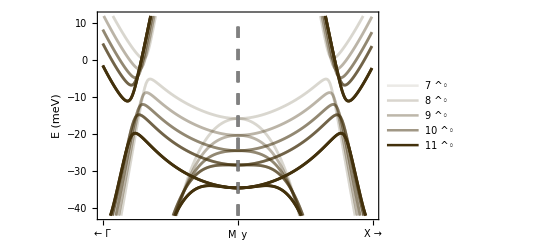

```mathematica
SpaghettiPlot1=Show[BandPlotList1]
```

### 2) Δ_nem=0.5%

```mathematica
BandDataList2=First@Last@Reap[Do[
HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],angle,0.5];

Sow[GenerateBandStructure[HamCurr,HSymmPts]];
,{angle,AngleList}]];
```

```mathematica
BandPlotList2=First@Last@Reap[Do[
Sow[PlotBandStructure[BandDataList2[[i]],{-42,12}(*meV range*),"AspectRatio"->3/5,"yLabel"->{(*Label*)"E (meV)",(*Font Size*)12,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{12,Black,"Arial"},"yTicks"->{9,Black,"Arial"},"LineThickness"->0.005,"LineColorScheme"->{RGBColor[ColourChoice[[1]],ColourChoice[[2]],ColourChoice[[3]],OpacityList[[i]]]},"PlotKeyLegend"->{Style[ToString[AngleList[[i]]],FontSize->8,FontFamily->"Times"],Scaled[{0.31,1.01-i/19.}]}]];
,{i,1,Length[AngleList]}]];
```

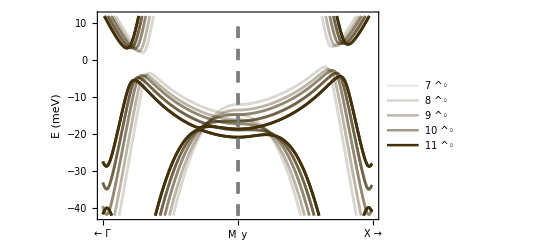

```mathematica
SpaghettiPlot2=Show[BandPlotList2]
```

### 3) Δ_nem=1%

```mathematica
BandDataList3=First@Last@Reap[Do[
HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],angle,1.];

Sow[GenerateBandStructure[HamCurr,HSymmPts]];
,{angle,AngleList}]];
```

```mathematica
BandPlotList3=First@Last@Reap[Do[
Sow[PlotBandStructure[BandDataList3[[i]],{-25,25}(*meV range*),"AspectRatio"->3/5,"yLabel"->{(*Label*)"E (meV)",(*Font Size*)12,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{12,Black,"Arial"},"yTicks"->{9,Black,"Arial"},"LineThickness"->0.005,"LineColorScheme"->{RGBColor[ColourChoice[[1]],ColourChoice[[2]],ColourChoice[[3]],OpacityList[[i]]]},"PlotKeyLegend"->{Style[ToString[AngleList[[i]]],FontSize->8,FontFamily->"Times"],Scaled[{0.31,1.01-i/19.}]}]];
,{i,1,Length[AngleList]}]];
```

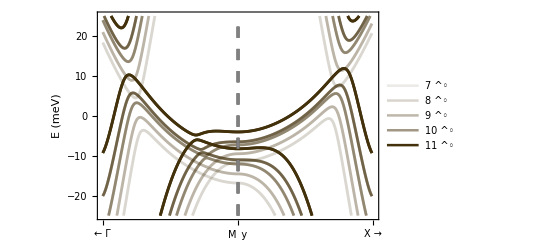

```mathematica
SpaghettiPlot3=Show[BandPlotList3]
```

### 3) Δ_nem=2%

```mathematica
BandDataList4=First@Last@Reap[Do[
HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],angle,2.];

Sow[GenerateBandStructure[HamCurr,HSymmPts]];
,{angle,AngleList}]];
```

```mathematica
BandPlotList4=First@Last@Reap[Do[
Sow[PlotBandStructure[BandDataList4[[i]],{-40,80}(*meV range*),"AspectRatio"->3/5,"yLabel"->{(*Label*)"E (meV)",(*Font Size*)12,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{12,Black,"Arial"},"yTicks"->{9,Black,"Arial"},"LineThickness"->0.005,"LineColorScheme"->{RGBColor[ColourChoice[[1]],ColourChoice[[2]],ColourChoice[[3]],OpacityList[[i]]]},"PlotKeyLegend"->{Style[ToString[AngleList[[i]]],FontSize->8,FontFamily->"Times"],Scaled[{0.31,1.01-i/19.}]}]];
,{i,1,Length[AngleList]}]];
```

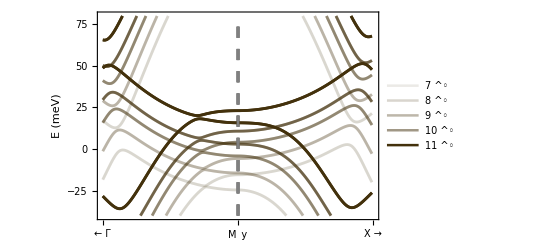

```mathematica
SpaghettiPlot4=Show[BandPlotList4]
```

```mathematica
NumberForm[{1000.3,34.56123,0.0034,1.4596},{3,3}]
```

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

{1000.000,34.600,0.003,1.460}

## Evolution of the nature of the critical points in the SOC gap

In this section, we look at the evolution of the nature of the critical points as we change Δ_nem and θ, that is whether they are maxima, minima or saddles.

### SOC gap upper VHS - Band 9

```mathematica
Do[
Print["Δ_nem=",Delt,"%:"];

Do[

HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θCurr,Delt];

kVHSTrialLow={0.6 3.869 0.36,π//N};
kVHSTrialUp={3.869 0.36,π//N};

(*Finding true kVHS:*)
{kVHS,CritPtFound}=LocateCriticalPoint[HamCurr,kVHSTrialLow,kVHSTrialUp,9,"Messages"->False,"SanityChecks"->True,"MaxIterations"->24,"Resolution"->10^-2];

If[CritPtFound==True,
TaylorPoly=Chop[Total[TaylorExpandBand[HamCurr,kVHS,9,2,"Messages"->False][[1]]]/.{p1->Subscript[k, x],p2->Subscript[k, y]},10^-2];

Print["\t","θ = ",θCurr,", k_crit = ",NumberForm[kVHS,{4,2}],", Tayl = ",NumberForm[TaylorPoly,{4,2}]];
,
Print["Critical point could not be found for θ = ",θCurr];
]

,{θCurr,8,11,1}];

,{Delt,{0,0.5,1,2}}];
```

Δ_nem=0%:

θ = 8, k_crit = {1.02,3.14}, Tayl = -2.36+529.00 k_x^2-9.48 k_y^2

θ = 9, k_crit = {1.06,3.14}, Tayl = -4.72+503.40 k_x^2+4.03 k_y^2

θ = 10, k_crit = {1.10,3.14}, Tayl = -6.73+483.80 k_x^2+16.24 k_y^2

θ = 11, k_crit = {1.14,3.14}, Tayl = -11.04+472.70 k_x^2+26.86 k_y^2

Δ_nem=0.5%:

θ = 8, k_crit = {1.01,3.14}, Tayl = 3.89+508.00 k_x^2-10.08 k_y^2

θ = 9, k_crit = {1.05,3.14}, Tayl = 4.46+485.60 k_x^2+3.54 k_y^2

θ = 10, k_crit = {1.09,3.14}, Tayl = 4.52+468.00 k_x^2+15.86 k_y^2

θ = 11, k_crit = {1.13,3.14}, Tayl = 4.30+458.10 k_x^2+26.58 k_y^2

Δ_nem=1%:

θ = 8, k_crit = {1.07,3.14}, Tayl = 11.38+416.20 k_x^2-13.27 k_y^2

θ = 9, k_crit = {1.11,3.14}, Tayl = 15.79+403.50 k_x^2-0.81 k_y^2

θ = 10, k_crit = {1.14,3.14}, Tayl = 18.87+398.80 k_x^2+10.21 k_y^2

θ = 11, k_crit = {1.18,3.14}, Tayl = 23.71+404.70 k_x^2+19.48 k_y^2

Δ_nem=2%:

θ = 8, k_crit = {1.25,3.14}, Tayl = 29.07+404.80 k_x^2-21.41 k_y^2

θ = 9, k_crit = {1.28,3.14}, Tayl = 42.04+404.60 k_x^2-12.77 k_y^2

θ = 10, k_crit = {1.31,3.14}, Tayl = 51.90+414.00 k_x^2-5.23 k_y^2

θ = 11, k_crit = {1.34,3.14}, Tayl = 67.46+432.80 k_x^2+1.15 k_y^2

We see that all the HOS points indeed likely lie in the range [8°,11°] since the coefficient of k_y^2 changes sign from - to + in this range for all the values of Δ_nem. Also, the critical point changes from an ordinary saddle to an ordinary minimum as we increase θ at each Δ_nem. Now for band 8 (downward dispersing):

### SOC gap lower VHS - Band 8

```mathematica
Do[
Print["Δ_nem=",Delt,"%:"];

Do[

HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θCurr,Delt];

kVHSTrialLow={0.5 3.869 0.35,π//N};
kVHSTrialUp={0.95 3.869 0.35,π//N};

(*Finding true kVHS:*)
{kVHS,CritPtFound}=LocateCriticalPoint[HamCurr,kVHSTrialLow,kVHSTrialUp,8,"Messages"->False,"SanityChecks"->False,"MaxIterations"->35,"Resolution"->10^-2];

If[CritPtFound==True,
TaylorPoly=Chop[Total[TaylorExpandBand[HamCurr,kVHS,8,2,"Messages"->False][[1]]]/.{p1->Subscript[k, x],p2->Subscript[k, y]},10^-2];

Print["\t","θ = ",θCurr,", k_crit = ",NumberForm[kVHS,{3,2}],", Tayl = ",NumberForm[TaylorPoly,{4,2}]];
,
Print["Critical point could not be found for θ = ",θCurr];
]

,{θCurr,8,12,1}];

,{Delt,{0,0.5,1,1.5}}];
```

Δ_nem=0%:

θ = 8, k_crit = {0.94,3.14}, Tayl = -8.71-417.40 k_x^2-12.35 k_y^2

θ = 9, k_crit = {0.98,3.14}, Tayl = -11.91-400.30 k_x^2+1.12 k_y^2

θ = 10, k_crit = {1.02,3.14}, Tayl = -14.71-388.40 k_x^2+13.20 k_y^2

θ = 11, k_crit = {1.06,3.14}, Tayl = -19.70-382.80 k_x^2+23.35 k_y^2

θ = 12, k_crit = {1.10,3.14}, Tayl = -20.80-380.60 k_x^2+30.68 k_y^2

Δ_nem=0.5%:

θ = 8, k_crit = {0.93,3.14}, Tayl = -2.43-395.90 k_x^2-12.99 k_y^2

θ = 9, k_crit = {0.97,3.14}, Tayl = -2.70-381.50 k_x^2+0.59 k_y^2

θ = 10, k_crit = {1.01,3.14}, Tayl = -3.43-371.80 k_x^2+12.79 k_y^2

θ = 11, k_crit = {1.05,3.14}, Tayl = -4.34-367.70 k_x^2+23.10 k_y^2

θ = 12, k_crit = {1.09,3.14}, Tayl = -5.34-366.50 k_x^2+30.63 k_y^2

Δ_nem=1%:

θ = 8, k_crit = {0.97,3.14}, Tayl = 2.27-310.20 k_x^2-16.77 k_y^2

θ = 9, k_crit = {1.01,3.14}, Tayl = 5.60-304.00 k_x^2-4.49 k_y^2

θ = 10, k_crit = {1.05,3.14}, Tayl = 7.73-304.80 k_x^2+6.01 k_y^2

θ = 11, k_crit = {1.09,3.14}, Tayl = 11.88-313.60 k_x^2+13.99 k_y^2

θ = 12, k_crit = {1.14,3.14}, Tayl = 12.20-329.70 k_x^2+18.32 k_y^2

Δ_nem=1.5%:

θ = 8, k_crit = {1.05,3.14}, Tayl = 7.28-293.30 k_x^2-20.74 k_y^2

θ = 9, k_crit = {1.09,3.14}, Tayl = 14.80-292.90 k_x^2-10.70 k_y^2

θ = 10, k_crit = {1.13,3.14}, Tayl = 20.46-301.10 k_x^2-2.82 k_y^2

θ = 11, k_crit = {1.17,3.14}, Tayl = 30.37-318.80 k_x^2+2.29 k_y^2

θ = 12, k_crit = {1.22,3.14}, Tayl = 32.64-346.60 k_x^2+4.02 k_y^2

Here too we see that for all the Δ_nem the HOS likely lies in the range [8°,12°]. Also, we see that the critical point changes from an ordinary maximum to an ordinary saddle as we increase θ at each Δ_nem up to 1.5%.

## Evolution of the nature of the critical points at the M point

When Δ_nem=0, we have a pair of degenerate bands that are 90° rotated with respect to each other. However, when Δ_nem!=0, the bands weakly split in energy. Since Δ_nem is small, we might still reasonably expect the bands to weakly preserve the π/2 rotation that was previously present. Nevertheless we will analyse the evolution of the Taylor expansion for both these bands separately.

### Lower VHS

```mathematica
Do[
Print["Δ_nem=",Delt,"%:"];

Do[

HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θCurr,Delt];


TaylorPoly=Chop[Total[TaylorExpandBand[HamCurr,{0,π//N},6,2,"Messages"->False][[1]]]/.{p1->Subscript[k, x],p2->Subscript[k, y]},10^-5];

Print["\t","θ = ",θCurr,", Tayl = ",Chop[NumberForm[TaylorPoly,{4,2}],10^-2]];


,{θCurr,8,12,1}];

,{Delt,{0.25,0.5,1,1.75}}];
```

Δ_nem=0.25%:

θ = 8, Tayl = -17.79-27.37 k_x^2+16.37 k_y^2

θ = 9, Tayl = -20.48-11.56 k_x^2+15.70 k_y^2

θ = 10, Tayl = -23.32+3.42 k_x^2+15.00 k_y^2

θ = 11, Tayl = -27.47+17.37 k_x^2+14.25 k_y^2

θ = 12, Tayl = -29.83+30.01 k_x^2+11.50 k_y^2

Δ_nem=0.5%:

θ = 8, Tayl = -16.08-27.77 k_x^2+16.56 k_y^2

θ = 9, Tayl = -17.16-12.08 k_x^2+15.90 k_y^2

θ = 10, Tayl = -18.82+2.79 k_x^2+15.21 k_y^2

θ = 11, Tayl = -20.78+16.61 k_x^2+14.48 k_y^2

θ = 12, Tayl = -22.94+29.09 k_x^2+11.79 k_y^2

Δ_nem=1%:

θ = 8, Tayl = -14.55-31.37 k_x^2+17.08 k_y^2

θ = 9, Tayl = -12.07-16.50 k_x^2+16.56 k_y^2

θ = 10, Tayl = -11.02-2.50 k_x^2+16.04 k_y^2

θ = 11, Tayl = -8.26+10.39 k_x^2+15.50 k_y^2

θ = 12, Tayl = -9.65+21.84 k_x^2+13.23 k_y^2

Δ_nem=1.75%:

θ = 8, Tayl = -14.45-38.72 k_x^2+18.60 k_y^2

θ = 9, Tayl = -6.16-26.19 k_x^2+18.44 k_y^2

θ = 10, Tayl = -0.57-14.58 k_x^2+18.34 k_y^2

θ = 11, Tayl = 9.72-4.16 k_x^2+18.30 k_y^2

θ = 12, Tayl = 9.88+4.74 k_x^2+17.04 k_y^2

We notice that the critical point evolves from a saddle to a minimum as θ increases for each Δ_nem since the sign of the coefficient of k_x^2 changes from - to + while the coefficient of k_y^2 remains positive throughout.

### Upper VHS

```mathematica
Do[
Print["Δ_nem=",Delt,"%:"];

Do[

HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θCurr,Delt];


TaylorPoly=Chop[Total[TaylorExpandBand[HamCurr,{0,π//N},8,2,"Messages"->False][[1]]]/.{p1->Subscript[k, x],p2->Subscript[k, y]},10^-5];

Print["\t","θ = ",θCurr,", Tayl = ",Chop[NumberForm[TaylorPoly,{4,2}],10^-2]];


,{θCurr,8,12,1}];

,{Delt,{0.25,0.5,1,1.75}}];
```

Δ_nem=0.25%:

θ = 8, Tayl = -16.47+16.03 k_x^2-27.76 k_y^2

θ = 9, Tayl = -19.23+15.38 k_x^2-11.94 k_y^2

θ = 10, Tayl = -22.13+14.69 k_x^2+3.08 k_y^2

θ = 11, Tayl = -26.36+13.96 k_x^2+17.05 k_y^2

θ = 12, Tayl = -28.81+11.23 k_x^2+29.73 k_y^2

Δ_nem=0.5%:

θ = 8, Tayl = -13.44+15.87 k_x^2-28.57 k_y^2

θ = 9, Tayl = -14.66+15.25 k_x^2-12.83 k_y^2

θ = 10, Tayl = -16.46+14.60 k_x^2+2.09 k_y^2

θ = 11, Tayl = -18.58+13.90 k_x^2+15.97 k_y^2

θ = 12, Tayl = -20.91+11.25 k_x^2+28.53 k_y^2

Δ_nem=1%:

θ = 8, Tayl = -9.51+15.74 k_x^2-33.11 k_y^2

θ = 9, Tayl = -7.29+15.28 k_x^2-18.13 k_y^2

θ = 10, Tayl = -6.51+14.81 k_x^2-3.98 k_y^2

θ = 11, Tayl = -4.05+14.34 k_x^2+9.05 k_y^2

θ = 12, Tayl = -5.78+12.15 k_x^2+20.67 k_y^2

Δ_nem=1.75%:

θ = 8, Tayl = -6.53+16.39 k_x^2-41.95 k_y^2

θ = 9, Tayl = 1.36+16.32 k_x^2-29.18 k_y^2

θ = 10, Tayl = 6.50+16.30 k_x^2-17.30 k_y^2

θ = 11, Tayl = 16.34+16.37 k_x^2-6.57 k_y^2

θ = 12, Tayl = 15.99+15.23 k_x^2+2.68 k_y^2

In this case as well, the critical point evolves from a saddle to a minimum as θ increases for each Δ_nem since the coefficient of the k_x^2 term remains positive while the coefficient of the k_y^2 term change sign from - to +. Furthermore, we notice that as we expected, there is only a weak breaking of the π/2 rotation when we compare the series expansion of the lower and upper VHS at the M point. For example the series expansion at Δ_nem=0.25% and θ=9° for the pair of bands respectively reads
"-20.48"-"11.56" k_x^("2")+"15.70" k_y^("2")
"-19.23"+"15.38" k_x^("2")-"11.94" k_y^("2")
These are still “approximately” related by the transformation (k_x,k_y)->(-k_y,k_x).

## Using binary search to find HOVHs in the SOC gap

### Band 9, part 1

```mathematica
NoIterns=5;
CurrResln=10^-2;
kVHSTrialLow={0.6 3.869 0.36,π//N};
kVHSTrialUp={3.869 0.36,π//N};

HosListBand9={};
SetSharedVariable[HosListBand9];

ParallelDo[
HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],k[[3]],Delt];

NoTry=0;
HOSFound=False;
HOSPossible=True;
θmax=11;
θmin=8;

(*Print["Binary search initiated for Δ_nem = ",Delt];*)

While[NoTry<=14&&HOSFound==False&&HOSPossible==True,
HamCurrUp[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmax,Delt];
HamCurrDown[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmin,Delt];

(*We compute the Hessian determinant for Subscript[θ, max]*)
(*Finding true kVHS:*)
{kVHSmax,CritPtFound}=LocateCriticalPoint[HamCurrUp,kVHSTrialLow,kVHSTrialUp,9,"Messages"->False,"SanityChecks"->True,"MaxIterations"->24,"Resolution"->10^-2];

TaylorPolyMax=TaylorExpandBand[HamCurrUp,kVHSmax,9,2,"Messages"->False];

If[CritPtFound==False,
HOSPossible=False;
];

TaylorPolyMax=Chop[TaylorPolyMax,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMax=(D[TaylorPolyMax[[1,3]],{p1,2}]D[TaylorPolyMax[[1,3]],{p2,2}]-(D[TaylorPolyMax[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

(*We now compute the Hessian determinant for Subscript[θ, min]*)
(*Finding true kVHS:*)
{kVHSmin,CritPtFound}=LocateCriticalPoint[HamCurrDown,kVHSTrialLow,kVHSTrialUp,9,"Messages"->False,"SanityChecks"->True,"MaxIterations"->24,"Resolution"->10^-2];

TaylorPolyMin=TaylorExpandBand[HamCurrDown,kVHSmin,9,2,"Messages"->False];

If[CritPtFound==False,
HOSPossible=False;
];

TaylorPolyMin=Chop[TaylorPolyMin,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMin=(D[TaylorPolyMin[[1,3]],{p1,2}]D[TaylorPolyMin[[1,3]],{p2,2}]-(D[TaylorPolyMin[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

(*Now we begin the binary search if the Hessian determinants computed above are opposite in sign*)
If[Sign[HesDetMax]==-Sign[HesDetMin]&&HOSFound==False&&HOSPossible==True,

θmid=0.5(θmax+θmin);
HamCurrMid[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmid,Delt];

(*Finding true kVHS1:*)
{kVHSmid,CritPtFound}=LocateCriticalPoint[HamCurrMid,kVHSTrialLow,kVHSTrialUp,9,"Messages"->False,"SanityChecks"->True,"MaxIterations"->24,"Resolution"->10^-2];

TaylorPolyMid=TaylorExpandBand[HamCurrMid,kVHSmid,9,2,"Messages"->False];

If[CritPtFound==False,
HOSPossible=False;
];

TaylorPolyMid=Chop[TaylorPolyMid,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMid=(D[TaylorPolyMid[[1,3]],{p1,2}]D[TaylorPolyMid[[1,3]],{p2,2}]-(D[TaylorPolyMid[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[CritPtFound==False,
HOSPossible=False;
];

TaylorPolyMid=Chop[TaylorPolyMid,CurrResln];

HesDet=(D[TaylorPolyMid[[1,3]],{p1,2}]D[TaylorPolyMid[[1,3]],{p2,2}]-(D[TaylorPolyMid[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[Chop[HesDet,1.]==0,
HOSFound=True;
,
If[Sign[HesDet]==Sign[HesDetMax],
θmax=θmid;
,
If[Sign[HesDet]==Sign[HesDetMin],
θmin=θmid;
]
]
];

NoTry++;
,
If[HOSFound==False,
Print[Style["No HOS in the range!",Red]];
HOSPossible=False;
]
];
];

If[HOSFound==True,
AppendTo[HosListBand9,{Delt,θmid,NoTry,kVHSmid}];
,
Print[Style["No HOS in the range!",Red]];
];
,{Delt,0,2,0.25}]
```

Since the list was constructed with a parallelized Do loop, we need to sort it

```mathematica
HosListBand9=SortBy[HosListBand9,First];
```

We are now in a position to examine the series expansion of the HOVHS for the critical tuning situations obtained above

```mathematica
Do[
HamCurrHOS[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],hosdata[[2]],hosdata[[1]]];
TaylorPolyHOS=TaylorExpandBand[HamCurrHOS,hosdata[[4]],9,4,"Messages"->False];

Print["Δ_nem = ",hosdata[[1]],". Binary search converged after ",hosdata[[3]]," iterations."];
Print["\t","θ_crit=",NumberForm[hosdata[[2]],{4,2}],", Tayl = ",NumberForm[Chop[Total[TaylorPolyHOS[[1]]]/.{p1->Subscript[k, x],p2->Subscript[k, y]},10^-2],{6,2}]];
DiagnoseHOS[Chop[Total[TaylorPolyHOS[[1]]],10^-2]];
Print["********************************************************************"]
,{hosdata,HosListBand9}]
```

Δ_nem = 0.. Binary search converged after 11 iterations.

θ_crit=8.70, Tayl = -4.09+510.83 k_x^2-4716.23 k_x^3+23497.90 k_x^4-116.26 k_x k_y^2+1997.04 k_x^2 k_y^2-73.75 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 0.25. Binary search converged after 7 iterations.

θ_crit=8.68, Tayl = -0.22+524.97 k_x^2-5211.00 k_x^3+29212.00 k_x^4+0.05 k_x^3 k_y-118.23 k_x k_y^2+2195.08 k_x^2 k_y^2-74.55 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 0.5. Binary search converged after 11 iterations.

θ_crit=8.73, Tayl = 4.23+491.34 k_x^2-4475.94 k_x^3+22621.60 k_x^4+0.08 k_x^3 k_y-111.84 k_x k_y^2+1914.84 k_x^2 k_y^2-74.38 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 0.75. Binary search converged after 11 iterations.

θ_crit=8.86, Tayl = 9.57+440.23 k_x^2-3323.17 k_x^3+12723.50 k_x^4+0.04 k_x^3 k_y-104.19 k_x k_y^2+1462.58 k_x^2 k_y^2-72.74 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.. Binary search converged after 11 iterations.

θ_crit=9.07, Tayl = 16.11+402.83 k_x^2-2464.46 k_x^3+6242.84 k_x^4-0.02 k_x^3 k_y-103.28 k_x k_y^2+1117.78 k_x^2 k_y^2-68.83 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.25. Binary search converged after 11 iterations.

θ_crit=9.36, Tayl = 24.22+385.65 k_x^2-1930.96 k_x^3+2457.90 k_x^4+0.01 k_x^2 k_y-0.09 k_x^3 k_y-110.85 k_x k_y^2+892.90 k_x^2 k_y^2-62.33 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.5. Binary search converged after 11 iterations.

θ_crit=9.74, Tayl = 33.82+386.60 k_x^2-1607.31 k_x^3-124.87 k_x^4+0.01 k_x^2 k_y-0.14 k_x^3 k_y-126.96 k_x k_y^2+742.99 k_x^2 k_y^2-0.01 k_x k_y^3-53.18 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.75. Binary search converged after 9 iterations.

θ_crit=10.26, Tayl = 44.42+402.43 k_x^2-1405.95 k_x^3-2426.43 k_x^4-0.01 k_x^2 k_y-0.03 k_x^3 k_y-151.17 k_x k_y^2+623.55 k_x^2 k_y^2-0.01 k_x k_y^3-41.76 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 2.. Binary search converged after 9 iterations.

θ_crit=10.85, Tayl = 62.25+429.31 k_x^2-1253.64 k_x^3-5084.61 k_x^4+0.09 k_x^3 k_y-183.41 k_x k_y^2+515.60 k_x^2 k_y^2-28.19 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

```mathematica
HosListBand9[[All,1;;2]]
```

{{0.,8.6958},{0.25,8.67969},{0.5,8.73389},{0.75,8.86279},{1.,9.06787},{1.25,9.35791},{1.5,9.7417},{1.75,10.2559},{2.,10.8535}}

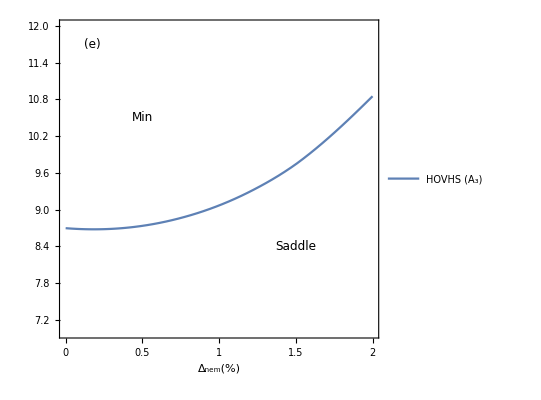

```mathematica
FitFunc1=Interpolation[HosListBand9[[All,1;;2]]];
PlotBand9=ListPlot[HosListBand9[[All,1;;2]]];
PanelE=Show[Plot[FitFunc1[x],{x,0,2},FrameLabel->{"Δ_nem(%)",(*"θ(°)"*)None},PlotLegends->Placed[{Style["HOVHS (A_3)",FontFamily->"Arial",FontSize->10]},{0.6,0.92}],PlotRange->{{0,2},{7,12}},Frame->True,AspectRatio->1,FrameTicks->{{Automatic,None},{{0,0.5,1,1.5,2},None}}],Graphics[Text[Style["Saddle",FontFamily->"Arial",FontSize->12],{1.5,8.4}]],Graphics[Text[Style["Min",FontFamily->"Arial",FontSize->12],{0.5,10.5}]],Graphics[Text[Style["(e)",FontFamily->"Arial",FontSize->12],{0.175,11.7}]](*,PlotBand9*)]
```

### Band 8, part 1

```mathematica
NoIterns=5;
CurrResln=10^-2;
kVHSTrialLow={0.5 3.869 0.35,π//N};
kVHSTrialUp={0.95 3.869 0.35,π//N};

HosListBand8={};
SetSharedVariable[HosListBand8];

ParallelDo[
HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],k[[3]],Delt];

NoTry=0;
HOSFound=False;
HOSPossible=True;
θmax=12;
θmin=8;

(*Print["Binary search initiated for Δ_nem = ",Delt];*)

While[NoTry<=18&&HOSFound==False&&HOSPossible==True,
HamCurrUp[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmax,Delt];
HamCurrDown[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmin,Delt];

(*We compute the Hessian determinant for Subscript[θ, max]*)
(*Finding true kVHS:*)
{kVHSmax,CritPtFound}=LocateCriticalPoint[HamCurrUp,kVHSTrialLow,kVHSTrialUp,8,"Messages"->False,"SanityChecks"->True,"MaxIterations"->28,"Resolution"->10^-2];

TaylorPolyMax=TaylorExpandBand[HamCurrUp,kVHSmax,8,2,"Messages"->False];
TaylorPolyMax=Chop[TaylorPolyMax,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMax=(D[TaylorPolyMax[[1,3]],{p1,2}]D[TaylorPolyMax[[1,3]],{p2,2}]-(D[TaylorPolyMax[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[CritPtFound==False,
HOSPossible=False;
(*Print["Critical point not found for θ_max at Δ_nem = ",Delt,"."];*)
];


(*We now compute the Hessian determinant for Subscript[θ, min]*)
(*Finding true kVHS:*)
{kVHSmin,CritPtFound}=LocateCriticalPoint[HamCurrDown,kVHSTrialLow,kVHSTrialUp,8,"Messages"->False,"SanityChecks"->True,"MaxIterations"->28,"Resolution"->10^-2];

TaylorPolyMin=TaylorExpandBand[HamCurrDown,kVHSmin,8,2,"Messages"->False];
TaylorPolyMin=Chop[TaylorPolyMin,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMin=(D[TaylorPolyMin[[1,3]],{p1,2}]D[TaylorPolyMin[[1,3]],{p2,2}]-(D[TaylorPolyMin[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[CritPtFound==False,
HOSPossible=False;
(*Print["Critical point not found for θ_min at Δ_nem = ",Delt,"."];*)
];

(*Now we begin the binary search if the Hessian determinants computed above are opposite in sign*)
If[Sign[HesDetMax]==-Sign[HesDetMin]&&HOSFound==False&&HOSPossible==True,

θmid=0.5(θmax+θmin);
HamCurrMid[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmid,Delt];

(*Finding true kVHS1:*)
{kVHSmid,CritPtFound}=LocateCriticalPoint[HamCurrMid,kVHSTrialLow,kVHSTrialUp,8,"Messages"->False,"SanityChecks"->True,"MaxIterations"->28,"Resolution"->10^-2];

TaylorPolyMid=TaylorExpandBand[HamCurrMid,kVHSmid,8,2,"Messages"->False];
TaylorPolyMid=Chop[TaylorPolyMid,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMid=(D[TaylorPolyMid[[1,3]],{p1,2}]D[TaylorPolyMid[[1,3]],{p2,2}]-(D[TaylorPolyMid[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[CritPtFound==False,
HOSPossible=False;
(*Print["Critical point not found for θ_mid at Δ_nem = ",Delt,"."];*)
];


If[Chop[HesDetMid,1.]==0,
HOSFound=True;
,
If[Sign[HesDetMid]==Sign[HesDetMax],
θmax=θmid;
,
If[Sign[HesDetMid]==Sign[HesDetMin],
θmin=θmid;
]
]
];

NoTry++;
,
If[HOSFound==False,
Print[Style["No HOS in the range!",Red]];
HOSPossible=False;
]
];
];

If[HOSFound==True,
AppendTo[HosListBand8,{Delt,θmid,NoTry,kVHSmid}];
,
Print[Style["No HOS in the range!",Red]];
];
,{Delt,0,1.5,0.25}]
```

```mathematica
HosListBand8=SortBy[HosListBand8,First];
```

```mathematica
Do[
HamCurrHOS[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],hosdata[[2]],hosdata[[1]]];
TaylorPolyHOS=TaylorExpandBand[HamCurrHOS,hosdata[[4]],8,4,"Messages"->False];

Print["Δ_nem = ",hosdata[[1]],". Binary search converged after ",hosdata[[3]]," iterations."];
Print["\t","θ_crit=",NumberForm[hosdata[[2]],{4,2}],", Tayl = ",NumberForm[Chop[Total[TaylorPolyHOS[[1]]]/.{p1->Subscript[k, x],p2->Subscript[k, y]},10^-2],{6,2}]];
DiagnoseHOS[Chop[Total[TaylorPolyHOS[[1]]],10^-2]];
Print["********************************************************************"]
,{hosdata,HosListBand8}]
```

Δ_nem = 0.. Binary search converged after 9 iterations.

θ_crit=8.91, Tayl = -11.66-401.64 k_x^2-4209.66 k_x^3-25725.60 k_x^4+117.43 k_x k_y^2+1457.44 k_x^2 k_y^2-86.96 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 0.25. Binary search converged after 11 iterations.

θ_crit=8.88, Tayl = -6.94-414.45 k_x^2-4642.84 k_x^3-31225.00 k_x^4+121.33 k_x k_y^2+1605.98 k_x^2 k_y^2-88.42 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 0.5. Binary search converged after 11 iterations.

θ_crit=8.96, Tayl = -2.70-382.06 k_x^2-3966.23 k_x^3-24498.20 k_x^4+113.62 k_x k_y^2+1381.22 k_x^2 k_y^2-87.38 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 0.75. Binary search converged after 5 iterations.

θ_crit=9.13, Tayl = 1.66-334.73 k_x^2-2939.67 k_x^3-14578.00 k_x^4+101.17 k_x k_y^2+1040.56 k_x^2 k_y^2-84.05 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.. Binary search converged after 10 iterations.

θ_crit=9.39, Tayl = 6.87-302.99 k_x^2-2204.97 k_x^3-8045.38 k_x^4-0.02 k_x^3 k_y+91.00 k_x k_y^2+807.63 k_x^2 k_y^2-78.27 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.25. Binary search converged after 10 iterations.

θ_crit=9.80, Tayl = 13.44-294.24 k_x^2-1773.94 k_x^3-3998.47 k_x^4-0.09 k_x^3 k_y+83.39 k_x k_y^2+688.22 k_x^2 k_y^2-69.12 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.5. Binary search converged after 6 iterations.

θ_crit=10.56, Tayl = 22.82-310.42 k_x^2-1508.70 k_x^3-360.33 k_x^4-0.01 k_x k_y-0.01 k_x^2 k_y+0.14 k_x^3 k_y+71.60 k_x k_y^2+648.09 k_x^2 k_y^2+0.02 k_x k_y^3-54.10 k_y^4

Polynomial has corank 1. It is 2-determinate. Its determinacy is either 2 or 1 and its codimension is 1. Comparing with the known list of singularities:

Point singularity has a finite determinacy but cannot identified by name!

********************************************************************

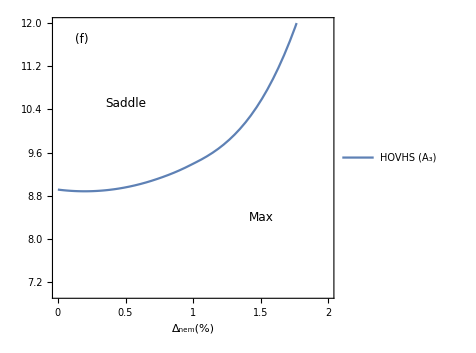

```mathematica
FitFunc2=Interpolation[HosListBand8[[All,1;;2]]];
PlotBand8=ListPlot[HosListBand8[[All,1;;2]]];
PanelF=Show[Plot[FitFunc2[x],{x,0,2},FrameLabel->{"Δ_nem(%)",(*"θ(°)"*)None},PlotLegends->Placed[{Style["HOVHS (A_3)",FontFamily->"Arial",FontSize->10]},{0.6,0.92}],PlotRange->{{0,2},{7,12}},Frame->True,AspectRatio->1,FrameTicks->{{Automatic,None},{{0,0.5,1,1.5,2},None}}],Graphics[Text[Style["Max",FontFamily->"Arial",FontSize->12],{1.5,8.4}]],Graphics[Text[Style["Saddle",FontFamily->"Arial",FontSize->12],{0.5,10.5}]],Graphics[Text[Style["(f)",FontFamily->"Arial",FontSize->12],{0.175,11.7}]](*,PlotBand8*)]
```

### Band 9, part 2

```mathematica
NoIterns=5;
CurrResln=10^-2;
kVHSTrialLow={0,π-3.869 0.36};
kVHSTrialUp={0,π-0.6 3.869 0.36};

HosListBand9p2={};
SetSharedVariable[HosListBand9p2];

ParallelDo[
HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],k[[3]],Delt];

NoTry=0;
HOSFound=False;
HOSPossible=True;
θmax=11;
θmin=8;

(*Print["Binary search initiated for Δ_nem = ",Delt];*)

While[NoTry<=14&&HOSFound==False&&HOSPossible==True,
HamCurrUp[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmax,Delt];
HamCurrDown[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmin,Delt];

(*We compute the Hessian determinant for Subscript[θ, max]*)
(*Finding true kVHS:*)
{kVHSmax,CritPtFound}=LocateCriticalPoint[HamCurrUp,kVHSTrialLow,kVHSTrialUp,9,"Messages"->False,"SanityChecks"->True,"MaxIterations"->24,"Resolution"->10^-2];

TaylorPolyMax=TaylorExpandBand[HamCurrUp,kVHSmax,9,2,"Messages"->False];

If[CritPtFound==False,
HOSPossible=False;
];

TaylorPolyMax=Chop[TaylorPolyMax,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMax=(D[TaylorPolyMax[[1,3]],{p1,2}]D[TaylorPolyMax[[1,3]],{p2,2}]-(D[TaylorPolyMax[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

(*We now compute the Hessian determinant for Subscript[θ, min]*)
(*Finding true kVHS:*)
{kVHSmin,CritPtFound}=LocateCriticalPoint[HamCurrDown,kVHSTrialLow,kVHSTrialUp,9,"Messages"->False,"SanityChecks"->True,"MaxIterations"->24,"Resolution"->10^-2];

TaylorPolyMin=TaylorExpandBand[HamCurrDown,kVHSmin,9,2,"Messages"->False];

If[CritPtFound==False,
HOSPossible=False;
];

TaylorPolyMin=Chop[TaylorPolyMin,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMin=(D[TaylorPolyMin[[1,3]],{p1,2}]D[TaylorPolyMin[[1,3]],{p2,2}]-(D[TaylorPolyMin[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

(*Now we begin the binary search if the Hessian determinants computed above are opposite in sign*)
If[Sign[HesDetMax]==-Sign[HesDetMin]&&HOSFound==False&&HOSPossible==True,

θmid=0.5(θmax+θmin);
HamCurrMid[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmid,Delt];

(*Finding true kVHS1:*)
{kVHSmid,CritPtFound}=LocateCriticalPoint[HamCurrMid,kVHSTrialLow,kVHSTrialUp,9,"Messages"->False,"SanityChecks"->True,"MaxIterations"->24,"Resolution"->10^-2];

TaylorPolyMid=TaylorExpandBand[HamCurrMid,kVHSmid,9,2,"Messages"->False];

If[CritPtFound==False,
HOSPossible=False;
];

TaylorPolyMid=Chop[TaylorPolyMid,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMid=(D[TaylorPolyMid[[1,3]],{p1,2}]D[TaylorPolyMid[[1,3]],{p2,2}]-(D[TaylorPolyMid[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[CritPtFound==False,
HOSPossible=False;
];

TaylorPolyMid=Chop[TaylorPolyMid,CurrResln];

HesDet=(D[TaylorPolyMid[[1,3]],{p1,2}]D[TaylorPolyMid[[1,3]],{p2,2}]-(D[TaylorPolyMid[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[Chop[HesDet,1.]==0,
HOSFound=True;
,
If[Sign[HesDet]==Sign[HesDetMax],
θmax=θmid;
,
If[Sign[HesDet]==Sign[HesDetMin],
θmin=θmid;
]
]
];

NoTry++;
,
If[HOSFound==False,
Print[Style["No HOS in the range!",Red]];
HOSPossible=False;
]
];
];

If[HOSFound==True,
AppendTo[HosListBand9p2,{Delt,θmid,NoTry,kVHSmid}];
,
Print[Style["No HOS in the range!",Red]];
];
,{Delt,0,2,0.25}]
```

```mathematica
HosListBand9p2=SortBy[HosListBand9p2,First];
```

```mathematica
Do[
HamCurrHOS[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],hosdata[[2]],hosdata[[1]]];
TaylorPolyHOS=TaylorExpandBand[HamCurrHOS,hosdata[[4]],9,4,"Messages"->False];

Print["Δ_nem = ",hosdata[[1]],". Binary search converged after ",hosdata[[3]]," iterations."];
Print["\t","θ_crit=",NumberForm[hosdata[[2]],{4,2}],", Tayl = ",NumberForm[Chop[Total[TaylorPolyHOS[[1]]]/.{p1->Subscript[k, x],p2->Subscript[k, y]},10^-2],{6,2}]];
DiagnoseHOS[Chop[Total[TaylorPolyHOS[[1]]],10^-2]];
Print["********************************************************************"]
,{hosdata,HosListBand9p2}]
```

Δ_nem = 0.. Binary search converged after 11 iterations.

θ_crit=8.70, Tayl = -4.09-73.75 k_x^4+116.26 k_x^2 k_y+510.83 k_y^2+1997.04 k_x^2 k_y^2+4716.23 k_y^3+23497.90 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 0.25. Binary search converged after 11 iterations.

θ_crit=8.64, Tayl = -0.88-73.87 k_x^4+123.15 k_x^2 k_y+546.36 k_y^2+2294.10 k_x^2 k_y^2+5496.38 k_y^3-0.06 k_x k_y^3+30376.60 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 0.5. Binary search converged after 5 iterations.

θ_crit=8.66, Tayl = 2.83-73.08 k_x^4+120.97 k_x^2 k_y+531.17 k_y^2+2084.18 k_x^2 k_y^2+4968.16 k_y^3-0.10 k_x k_y^3+24333.20 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 0.75. Binary search converged after 10 iterations.

θ_crit=8.75, Tayl = 7.37-70.86 k_x^4+116.16 k_x^2 k_y+491.11 k_y^2+1644.82 k_x^2 k_y^2+3853.39 k_y^3-0.08 k_x k_y^3+13891.20 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.. Binary search converged after 9 iterations.

θ_crit=8.92, Tayl = 13.15-66.45 k_x^4+117.07 k_x^2 k_y+460.17 k_y^2+1281.90 k_x^2 k_y^2+2955.17 k_y^3-0.02 k_x k_y^3+6573.65 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.25. Binary search converged after 10 iterations.

θ_crit=9.18, Tayl = 20.68-59.43 k_x^4+126.62 k_x^2 k_y+448.43 k_y^2+1034.66 k_x^2 k_y^2+2371.82 k_y^3+0.06 k_x k_y^3+1964.09 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.5. Binary search converged after 11 iterations.

θ_crit=9.54, Tayl = 30.18-49.76 k_x^4+145.12 k_x^2 k_y+455.23 k_y^2+0.01 k_x k_y^2+860.97 k_x^2 k_y^2+2001.61 k_y^3+0.16 k_x k_y^3-1502.14 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.75. Binary search converged after 8 iterations.

θ_crit=10.03, Tayl = 41.06-37.73 k_x^4+172.51 k_x^2 k_y+0.02 k_x^3 k_y+478.47 k_y^2+0.01 k_x k_y^2+713.88 k_x^2 k_y^2+1757.47 k_y^3+0.18 k_x k_y^3-4928.18 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 2.. Binary search converged after 6 iterations.

θ_crit=10.67, Tayl = 55.76-23.62 k_x^4+209.31 k_x^2 k_y+0.01 k_x^3 k_y+516.06 k_y^2+554.24 k_x^2 k_y^2+1576.22 k_y^3-0.08 k_x k_y^3-9202.16 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

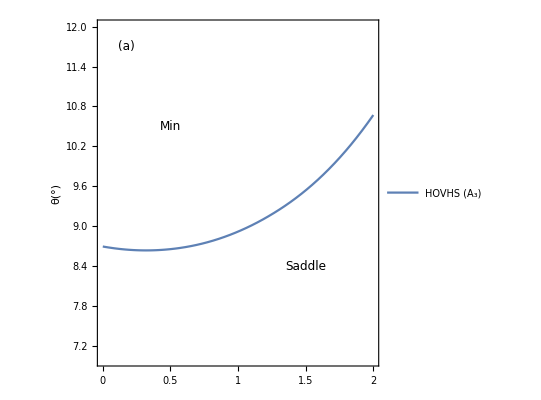

```mathematica
FitFunc3=Interpolation[HosListBand9p2[[All,1;;2]]];
PlotBand9p2=ListPlot[HosListBand9p2[[All,1;;2]]];
PanelA=Show[(*PlotBand9,*)Plot[FitFunc3[x],{x,0,2},FrameLabel->{(*"Δ_nem(%)"*)None,"θ(°)"},PlotLegends->Placed[{Style["HOVHS (A_3)",FontFamily->"Arial",FontSize->10]},{0.6,0.92}],PlotRange->{{0,2},{7,12}},Frame->True,AspectRatio->1,FrameTicks->{{Automatic,None},{{0,0.5,1,1.5,2},None}}],Graphics[Text[Style["Saddle",FontFamily->"Arial",FontSize->12],{1.5,8.4}]],Graphics[Text[Style["Min",FontFamily->"Arial",FontSize->12],{0.5,10.5}]],Graphics[Text[Style["(a)",FontFamily->"Arial",FontSize->12],{0.175,11.7}]]]
```

### Band 8, part 2

```mathematica
NoIterns=5;
CurrResln=10^-2;
kVHSTrialLow={0,π-0.95 3.869 0.35};
kVHSTrialUp={0,π-0.5 3.869 0.35};

HosListBand8p2={};
SetSharedVariable[HosListBand8p2];

ParallelDo[
HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],k[[3]],Delt];

NoTry=0;
HOSFound=False;
HOSPossible=True;
θmax=12;
θmin=8;

(*Print["Binary search initiated for Δ_nem = ",Delt];*)

While[NoTry<=18&&HOSFound==False&&HOSPossible==True,
HamCurrUp[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmax,Delt];
HamCurrDown[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmin,Delt];

(*We compute the Hessian determinant for Subscript[θ, max]*)
(*Finding true kVHS:*)
{kVHSmax,CritPtFound}=LocateCriticalPoint[HamCurrUp,kVHSTrialLow,kVHSTrialUp,8,"Messages"->False,"SanityChecks"->True,"MaxIterations"->28,"Resolution"->10^-2];

TaylorPolyMax=TaylorExpandBand[HamCurrUp,kVHSmax,8,2,"Messages"->False];
TaylorPolyMax=Chop[TaylorPolyMax,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMax=(D[TaylorPolyMax[[1,3]],{p1,2}]D[TaylorPolyMax[[1,3]],{p2,2}]-(D[TaylorPolyMax[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[CritPtFound==False,
HOSPossible=False;
(*Print["Critical point not found for θ_max at Δ_nem = ",Delt,"."];*)
];


(*We now compute the Hessian determinant for Subscript[θ, min]*)
(*Finding true kVHS:*)
{kVHSmin,CritPtFound}=LocateCriticalPoint[HamCurrDown,kVHSTrialLow,kVHSTrialUp,8,"Messages"->False,"SanityChecks"->True,"MaxIterations"->28,"Resolution"->10^-2];

TaylorPolyMin=TaylorExpandBand[HamCurrDown,kVHSmin,8,2,"Messages"->False];
TaylorPolyMin=Chop[TaylorPolyMin,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMin=(D[TaylorPolyMin[[1,3]],{p1,2}]D[TaylorPolyMin[[1,3]],{p2,2}]-(D[TaylorPolyMin[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[CritPtFound==False,
HOSPossible=False;
(*Print["Critical point not found for θ_min at Δ_nem = ",Delt,"."];*)
];

(*Now we begin the binary search if the Hessian determinants computed above are opposite in sign*)
If[Sign[HesDetMax]==-Sign[HesDetMin]&&HOSFound==False&&HOSPossible==True,

θmid=0.5(θmax+θmin);
HamCurrMid[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],θmid,Delt];

(*Finding true kVHS1:*)
{kVHSmid,CritPtFound}=LocateCriticalPoint[HamCurrMid,kVHSTrialLow,kVHSTrialUp,8,"Messages"->False,"SanityChecks"->True,"MaxIterations"->28,"Resolution"->10^-2];

TaylorPolyMid=TaylorExpandBand[HamCurrMid,kVHSmid,8,2,"Messages"->False];
TaylorPolyMid=Chop[TaylorPolyMid,CurrResln];

(*Print["k_(crit, max) = ",kVHSmax,TaylorPolyMax[[1]]];*)

HesDetMid=(D[TaylorPolyMid[[1,3]],{p1,2}]D[TaylorPolyMid[[1,3]],{p2,2}]-(D[TaylorPolyMid[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[CritPtFound==False,
HOSPossible=False;
(*Print["Critical point not found for θ_mid at Δ_nem = ",Delt,"."];*)
];


If[Chop[HesDetMid,1.]==0,
HOSFound=True;
,
If[Sign[HesDetMid]==Sign[HesDetMax],
θmax=θmid;
,
If[Sign[HesDetMid]==Sign[HesDetMin],
θmin=θmid;
]
]
];

NoTry++;
,
If[HOSFound==False,
Print[Style["No HOS in the range!",Red]];
HOSPossible=False;
]
];
];

If[HOSFound==True,
AppendTo[HosListBand8p2,{Delt,θmid,NoTry,kVHSmid}];
,
Print[Style["No HOS in the range!",Red]];
];
,{Delt,Append[Table[i,{i,0,1.5,0.25}],1.6]}]
```

```mathematica
HosListBand8p2=SortBy[HosListBand8p2,First];
```

```mathematica
Do[
HamCurrHOS[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],hosdata[[2]],hosdata[[1]]];
TaylorPolyHOS=TaylorExpandBand[HamCurrHOS,hosdata[[4]],8,4,"Messages"->False];

Print["Δ_nem = ",hosdata[[1]],". Binary search converged after ",hosdata[[3]]," iterations."];
Print["\t","θ_crit=",NumberForm[hosdata[[2]],{4,2}],", Tayl = ",NumberForm[Chop[Total[TaylorPolyHOS[[1]]]/.{p1->Subscript[k, x],p2->Subscript[k, y]},10^-2],{6,2}]];
DiagnoseHOS[Chop[Total[TaylorPolyHOS[[1]]],10^-2]];
Print["********************************************************************"]
,{hosdata,HosListBand8p2}]
```

Δ_nem = 0.. Binary search converged after 9 iterations.

θ_crit=8.91, Tayl = -11.66-86.96 k_x^4-117.43 k_x^2 k_y-401.64 k_y^2+1457.44 k_x^2 k_y^2+4209.66 k_y^3-25725.60 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 0.25. Binary search converged after 12 iterations.

θ_crit=8.84, Tayl = -7.58-88.03 k_x^4-125.54 k_x^2 k_y-435.67 k_y^2+1696.36 k_x^2 k_y^2+4929.44 k_y^3+0.01 k_x k_y^3-32820.80 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 0.5. Binary search converged after 11 iterations.

θ_crit=8.87, Tayl = -4.08-86.54 k_x^4-121.31 k_x^2 k_y-421.81 k_y^2+1536.27 k_x^2 k_y^2+4462.10 k_y^3+0.01 k_x k_y^3-26931.40 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 0.75. Binary search converged after 10 iterations.

θ_crit=9.00, Tayl = -0.46-82.65 k_x^4-110.74 k_x^2 k_y-385.56 k_y^2+1209.01 k_x^2 k_y^2+3471.89 k_y^3-16446.60 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.. Binary search converged after 10 iterations.

θ_crit=9.24, Tayl = 4.16-76.28 k_x^4-101.51 k_x^2 k_y-360.68 k_y^2+969.41 k_x^2 k_y^2+2694.18 k_y^3+0.02 k_x k_y^3-8873.05 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.25. Binary search converged after 10 iterations.

θ_crit=9.61, Tayl = 10.64-66.64 k_x^4-94.74 k_x^2 k_y-356.79 k_y^2+843.98 k_x^2 k_y^2+2193.99 k_y^3+0.12 k_x k_y^3-3645.34 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.5. Binary search converged after 9 iterations.

θ_crit=10.40, Tayl = 19.95-50.80 k_x^4-81.88 k_x^2 k_y-0.01 k_x^3 k_y-378.00 k_y^2+801.88 k_x^2 k_y^2+1832.04 k_y^3-0.08 k_x k_y^3+1691.74 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.6. Binary search converged after 10 iterations.

θ_crit=10.93, Tayl = 31.06-42.02 k_x^4-78.97 k_x^2 k_y-397.35 k_y^2+854.97 k_x^2 k_y^2+1649.95 k_y^3-0.08 k_x k_y^3+5058.27 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

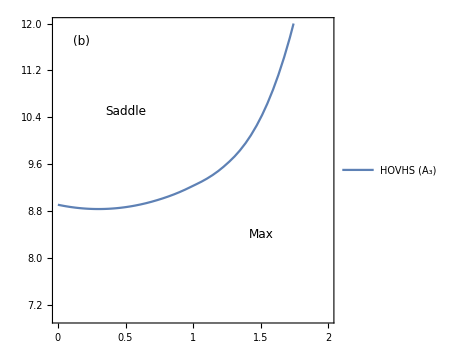

```mathematica
FitFunc4=Interpolation[HosListBand8p2[[All,1;;2]]];
PlotBand8p2=ListPlot[HosListBand8p2[[All,1;;2]]];
PanelB=Show[(*PlotBand9,*)Plot[FitFunc4[x],{x,0,2},FrameLabel->{(*"Δ_nem(%)"*)None,(*"θ(°)"*)None},PlotLegends->Placed[{Style["HOVHS (A_3)",FontFamily->"Arial",FontSize->10]},{0.6,0.92}],PlotRange->{{0,2},{7,12}},Frame->True,AspectRatio->1,FrameTicks->{{Automatic,None},{{0,0.5,1,1.5,2},None}}],Graphics[Text[Style["Max",FontFamily->"Arial",FontSize->12],{1.5,8.4}]],Graphics[Text[Style["Saddle",FontFamily->"Arial",FontSize->12],{0.5,10.5}]],Graphics[Text[Style["(b)",FontFamily->"Arial",FontSize->12],{0.175,11.7}]]]
```

## Finding HOVHs at the M point

### Upper VHS - Bands 7 & 8

```mathematica
HosListBand8M={};
SetSharedVariable[HosListBand8M];

ParallelDo[
HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],k[[3]],Delt];

θCurr=10.5;
CurrResln=10^-2;
HOSFound=False;
NoTry=1;

While[NoTry<=4&&HOSFound==False,
TaylorPoly=Chop[TaylorExpandBand[HamCurr(*The Hamiltonian*),{0,π//N,θCurr}(*the (k,t) point at which we are going to series expand.*),8(*Band to series expand*),2(*Degree of Taylor polynomial*),"Dimension"->2(*k-space dimension*),"TuningDegree"->2(*Degree of tuning parameter terms*),"TuningSymbol"->"δθ"(*Symbols for the tuning parameters*),"Resolution"->10^-4(*Resolution below which we shall kill terms*),"SampleDirection"->{0.333,0.779,0.1335}(*A sample k-vector that will be used for diagonalising symbolic matrices. This is not needed in principle since we will generate a random one in the routine if this is not provided*),"Messages"->False(*YesMessage*)],10^-6];

HesDet=(D[TaylorPoly[[1,3]],{p1,2}]D[TaylorPoly[[1,3]],{p2,2}]-(D[TaylorPoly[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[Chop[ReplaceAll[HesDet,{δθ->0}],CurrResln]==0,
HOSFound=True;
];

δθSolns=Solve[HesDet==0,δθ,Reals];

MinSoln=1;
Do[
If[Abs[ReplaceAll[δθ,δθSolns[[l]]]]<Abs[ReplaceAll[δθ,δθSolns[[MinSoln]]]],
MinSoln=l;
]
,{l,1,Length[δθSolns]}];

θCurr=θCurr+δθ/.δθSolns[[MinSoln]];
];

If[HOSFound==True,
TaylorPoly=Chop[TaylorExpandBand[HamCurr(*The Hamiltonian*),{0,π//N,θCurr}(*the (k,t) point at which we are going to series expand.*),8(*Band to series expand*),4(*Degree of Taylor polynomial*),"Dimension"->2(*k-space dimension*),"TuningDegree"->0(*Degree of tuning parameter terms*),"TuningSymbol"->"δθ"(*Symbols for the tuning parameters*),"Resolution"->10^-4(*Resolution below which we shall kill terms*),"SampleDirection"->{0.333,0.779,0.1335}(*A sample k-vector that will be used for diagonalising symbolic matrices. This is not needed in principle since we will generate a random one in the routine if this is not provided*),"Messages"->False(*YesMessage*)],10^-6];

AppendTo[HosListBand8M,{Delt,θCurr,NoTry,Total[Chop[ReplaceAll[TaylorPoly[[1]],{p1->Subscript[k, x],p2->Subscript[k, y],δθ->0}],CurrResln]]}];
,
Print[Style["No HOS found in the range!",Red]];
];

,{Delt,0,1.75,0.25}]
```

```mathematica
HosListBand8M=SortBy[HosListBand8M,First];
```

```mathematica
Do[
Print["Δ_nem = ",hosdata[[1]],". Search converged after ",hosdata[[3]]," iterations."];
Print["\t"<>"θ_crit = ",NumberForm[hosdata[[2]],{4,2}],", Tayl = ",NumberForm[hosdata[[4]],{3,2}]];
DiagnoseHOS[Chop[hosdata[[4]],10^-1]];
Print["********************************************************************"]

,{hosdata,HosListBand8M}]
```

Δ_nem = 0.. Search converged after 1 iterations.

θ_crit = 9.84, Tayl = -27.70-98.80 k_x^4+15.20 k_y^2+4.52 k_x^2 k_y^2-8.08 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 0.25. Search converged after 1 iterations.

θ_crit = 9.79, Tayl = -21.40+14.90 k_x^2-6.01 k_x^4+1.98 k_x^2 k_y^2-98.60 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 0.5. Search converged after 1 iterations.

θ_crit = 9.85, Tayl = -16.10+14.70 k_x^2-6.16 k_x^4+2.65 k_x^2 k_y^2-98.80 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 0.75. Search converged after 1 iterations.

θ_crit = 10.03, Tayl = -11.30+14.60 k_x^2-5.04 k_x^4+1.32 k_x^2 k_y^2-97.60 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.. Search converged after 1 iterations.

θ_crit = 10.30, Tayl = -6.93+14.60 k_x^2-2.98 k_x^4-0.01 k_x^3 k_y-1.37 k_x^2 k_y^2-95.10 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.25. Search converged after 1 iterations.

θ_crit = 10.68, Tayl = -1.12+14.80 k_x^2-0.23 k_x^4-0.02 k_x^3 k_y-5.33 k_x^2 k_y^2-91.10 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.5. Search converged after 1 iterations.

θ_crit = 11.09, Tayl = 12.10+15.70 k_x^2+2.54 k_x^4+0.01 k_x^3 k_y-10.30 k_x^2 k_y^2-84.20 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.75. Search converged after 1 iterations.

θ_crit = 11.44, Tayl = 33.90+17.20 k_x^2+5.17 k_x^4-0.03 k_x k_y+0.08 k_x^3 k_y-15.60 k_x^2 k_y^2-74.30 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

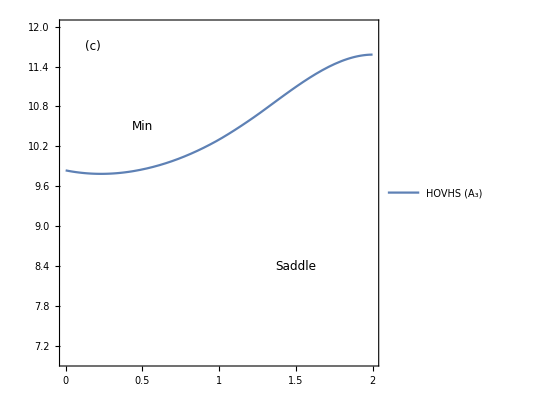

```mathematica
FitFunc5=Interpolation[HosListBand8M[[All,1;;2]]];
PlotBand8p3=ListPlot[HosListBand8M[[All,1;;2]],AxesLabel->{"Δ_nem(%)","θ(°)"},PlotLegends->Placed[{"HOVHs (A_3)"},{0.5,0.965}]];
PanelC=Show[(*PlotBand9,*)Plot[FitFunc5[x],{x,0,2},FrameLabel->{(*"Δ_nem(%)","θ(°)"*)None,None},PlotLegends->Placed[{Style["HOVHS (A_3)",FontFamily->"Arial",FontSize->10]},{0.6,0.92}],PlotRange->{{0,2},{7,12}},Frame->True,AspectRatio->1,FrameTicks->{{Automatic,None},{{0,0.5,1,1.5,2},None}}],Graphics[Text[Style["Saddle",FontFamily->"Arial",FontSize->12],{1.5,8.4}]],Graphics[Text[Style["Min",FontFamily->"Arial",FontSize->12],{0.5,10.5}]],Graphics[Text[Style["(c)",FontFamily->"Arial",FontSize->12],{0.175,11.7}]]]
```

### Lower VHS Bands 5 & 6

```mathematica
HosListBand6M={};
SetSharedVariable[HosListBand6M];

ParallelDo[
HamCurr[k_]:=HamiltonianNemTunedmeV[k[[1]],k[[2]],k[[3]],Delt];

θCurr=10.5;
CurrResln=10^-2;
HOSFound=False;
NoTry=1;

While[NoTry<=4&&HOSFound==False,
TaylorPoly=Chop[TaylorExpandBand[HamCurr(*The Hamiltonian*),{0,π//N,θCurr}(*the (k,t) point at which we are going to series expand.*),6(*Band to series expand*),2(*Degree of Taylor polynomial*),"Dimension"->2(*k-space dimension*),"TuningDegree"->2(*Degree of tuning parameter terms*),"TuningSymbol"->"δθ"(*Symbols for the tuning parameters*),"Resolution"->10^-4(*Resolution below which we shall kill terms*),"SampleDirection"->{0.333,0.779,0.1335}(*A sample k-vector that will be used for diagonalising symbolic matrices. This is not needed in principle since we will generate a random one in the routine if this is not provided*),"Messages"->False(*YesMessage*)],10^-6];

HesDet=(D[TaylorPoly[[1,3]],{p1,2}]D[TaylorPoly[[1,3]],{p2,2}]-(D[TaylorPoly[[1,3]],p1,p2])^2)/.{p1->0,p2->0}//Simplify;

If[Chop[ReplaceAll[HesDet,{δθ->0}],CurrResln]==0,
HOSFound=True;
];

δθSolns=Solve[HesDet==0,δθ,Reals];

MinSoln=1;
Do[
If[Abs[ReplaceAll[δθ,δθSolns[[l]]]]<Abs[ReplaceAll[δθ,δθSolns[[MinSoln]]]],
MinSoln=l;
]
,{l,1,Length[δθSolns]}];

θCurr=θCurr+δθ/.δθSolns[[MinSoln]];
];

If[HOSFound==True,
TaylorPoly=Chop[TaylorExpandBand[HamCurr(*The Hamiltonian*),{0,π//N,θCurr}(*the (k,t) point at which we are going to series expand.*),6(*Band to series expand*),4(*Degree of Taylor polynomial*),"Dimension"->2(*k-space dimension*),"TuningDegree"->0(*Degree of tuning parameter terms*),"TuningSymbol"->"δθ"(*Symbols for the tuning parameters*),"Resolution"->10^-4(*Resolution below which we shall kill terms*),"SampleDirection"->{0.333,0.779,0.1335}(*A sample k-vector that will be used for diagonalising symbolic matrices. This is not needed in principle since we will generate a random one in the routine if this is not provided*),"Messages"->False(*YesMessage*)],10^-6];

AppendTo[HosListBand6M,{Delt,θCurr,NoTry,Total[Chop[ReplaceAll[TaylorPoly[[1]],{p1->Subscript[k, x],p2->Subscript[k, y],δθ->0}],CurrResln]]}];
,
Print[Style["No HOS found in the range!",Red]];
];

,{Delt,0,1.75,0.25}]
```

```mathematica
HosListBand6M=SortBy[HosListBand6M,First];
```

```mathematica
Do[
Print["Δ_nem = ",hosdata[[1]],". Search converged after ",hosdata[[3]]," iterations."];
Print["\t"<>"θ_crit = ",NumberForm[hosdata[[2]],{4,2}],", Tayl = ",NumberForm[hosdata[[4]],{3,2}]];
DiagnoseHOS[Chop[hosdata[[4]],10^-1]];
Print["********************************************************************"]

,{hosdata,HosListBand6M}];
```

Δ_nem = 0.. Search converged after 1 iterations.

θ_crit = 9.84, Tayl = -27.70-98.80 k_x^4+15.20 k_y^2+4.52 k_x^2 k_y^2-8.08 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 0.25. Search converged after 1 iterations.

θ_crit = 9.76, Tayl = -22.50-101.00 k_x^4+15.20 k_y^2+7.55 k_x^2 k_y^2-8.87 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 0.5. Search converged after 1 iterations.

θ_crit = 9.81, Tayl = -18.30-100.00 k_x^4+15.40 k_y^2+6.40 k_x^2 k_y^2-8.20 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 0.75. Search converged after 1 iterations.

θ_crit = 9.95, Tayl = -14.70-99.50 k_x^4+15.60 k_y^2+6.24 k_x^2 k_y^2-7.77 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.. Search converged after 1 iterations.

θ_crit = 10.19, Tayl = -11.20-98.20 k_x^4+0.02 k_x^3 k_y+15.90 k_y^2+6.43 k_x^2 k_y^2-0.01 k_x k_y^3-7.26 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.25. Search converged after 1 iterations.

θ_crit = 10.53, Tayl = -7.09-96.30 k_x^4+0.03 k_x^3 k_y+16.30 k_y^2+7.02 k_x^2 k_y^2-0.02 k_x k_y^3-6.81 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.5. Search converged after 1 iterations.

θ_crit = 10.93, Tayl = 2.20-93.30 k_x^4+0.01 k_x^3 k_y+17.20 k_y^2+8.54 k_x^2 k_y^2-7.13 k_y^4

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

Δ_nem = 1.75. Search converged after 1 iterations.

θ_crit = 11.30, Tayl = 21.30-88.10 k_x^4-0.07 k_x^3 k_y+11.60 k_x^2 k_y^2+0.02 k_x k_y^3-8.72 k_y^4+k_y (0.02 k_x+18.80 k_y)

Polynomial has corank 1. It is 4-determinate. Its determinacy is either 4 or 3 and its codimension is 2. Comparing with the known list of singularities:

Polynomial has a cusp (A_3) catastrophe.

********************************************************************

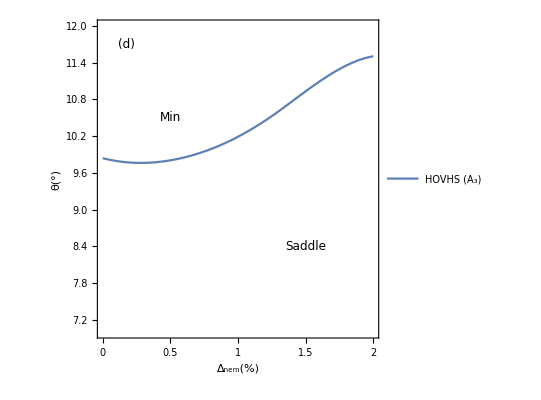

```mathematica
FitFunc6=Interpolation[HosListBand6M[[All,1;;2]]];
PlotBand6=ListPlot[HosListBand6M[[All,1;;2]],AxesLabel->{"Δ_nem(%)","θ(°)"},PlotLegends->Placed[{"HOVHs (A_3)"},{0.5,0.965}]];
PanelD=Show[(*PlotBand9,*)Plot[FitFunc6[x],{x,0,2},FrameLabel->{"Δ_nem(%)","θ(°)"},PlotLegends->Placed[{Style["HOVHS (A_3)",FontFamily->"Arial",FontSize->10]},{0.6,0.92}],PlotRange->{{0,2},{7,12}},Frame->True,AspectRatio->1,FrameTicks->{{Automatic,None},{{0,0.5,1,1.5,2},None}}],Graphics[Text[Style["Saddle",FontFamily->"Arial",FontSize->12],{1.5,8.4}]],Graphics[Text[Style["Min",FontFamily->"Arial",FontSize->12],{0.5,10.5}]],Graphics[Text[Style["(d)",FontFamily->"Arial",FontSize->12],{0.175,11.7}]]]
```

## Assembling the results

### Labeling the critical points of interest

```mathematica
Bnd4=GenerateBandStructure[HamTempNem2,HSymmPts,"OrbitalProjection"->True,"OrbitalGrouping"->{{1,4,7,10},{2,5,8,11},{3,6,9,12}}];
```

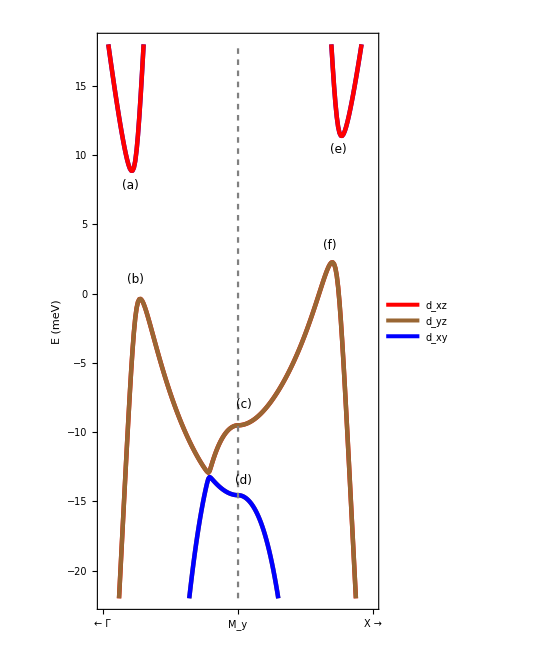

```mathematica
PltCritPts=PlotBandStructure[Bnd3,(*{-0.042,0.012}*){-22,18},AspectRatio->5/3,"yLabel"->{(*Label*)"E (meV)",(*Font Size*)13,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{13,Black,"Arial"},"yTicks"->{12,Black,"Helvetica"},"LineThickness"->0.008,"LineColorScheme"->{Red,Brown,Blue},(*Dividing Lines*)"DividingLines"->{(*Dashing[..]*)0.01,(*Color*)Gray,(*Thickness*)0.004},(*,Legend*)"PlotKeyLegend"->{{"d_xz","d_yz","d_xy"},{0.25,0.8}}];
PanelCritPts=Show[PltCritPts,Graphics[Text[Style["(a)",FontFamily->"Arial",FontSize->12],{0.28,7.8}]],Graphics[Text[Style["(b)",FontFamily->"Arial",FontSize->12],{0.34,1}]],Graphics[Text[Style["(c)",FontFamily->"Arial",FontSize->12],{1.45,-8}]],Graphics[Text[Style["(d)",FontFamily->"Arial",FontSize->12],{1.45,-13.5}]],Graphics[Text[Style["(e)",FontFamily->"Arial",FontSize->12],{2.43,10.42}]],Graphics[Text[Style["(f)",FontFamily->"Arial",FontSize->12],{2.34,3.5}]]]
```

### Phase diagrams for the critical points

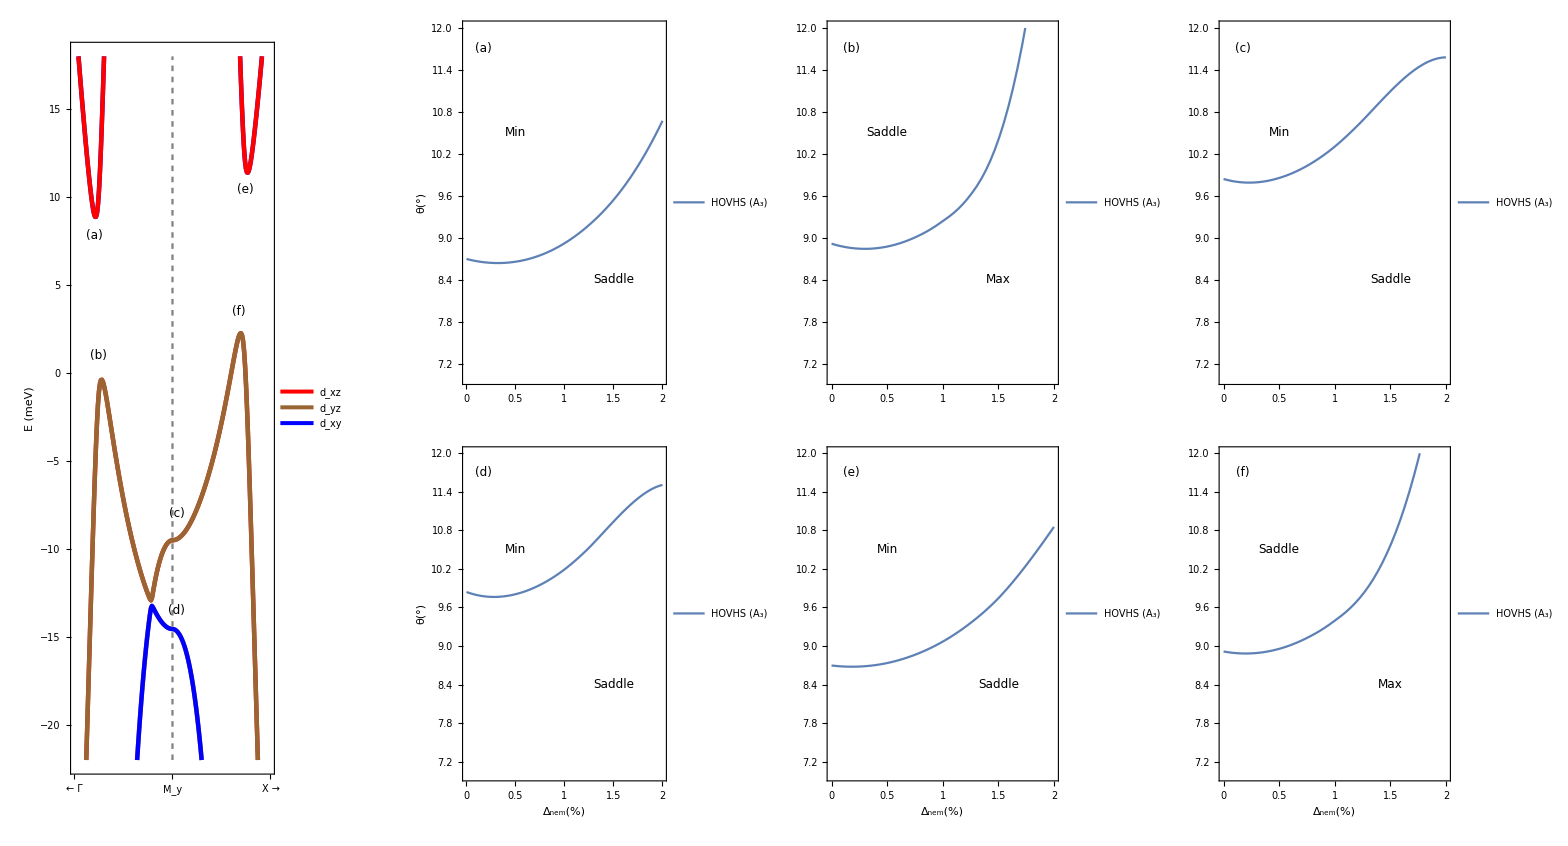

```mathematica
Show[GraphicsGrid[{{PanelCritPts,PanelA,PanelB,PanelC},{SpanFromAbove,PanelD,PanelE,PanelF}},Spacings->{Scaled[0.],Scaled[0.02]}],ImageSize->Full]
```

We can also examine the orbital-projected band structure in the absence of nematicity and compare with the nematic model

```mathematica
BndTemp=GenerateBandStructure[HamTemp,HSymmPts,"OrbitalProjection"->True,"OrbitalGrouping"->{{1,4,7,10},{2,5,8,11},{3,6,9,12}}];
```

```mathematica
PltTemp=PlotBandStructure[BndTemp,(*{-0.042,0.012}*){-28,18},AspectRatio->5/3,"yLabel"->{(*Label*)"E (meV)",(*Font Size*)13,(*Font Color*)Black,(*Font Family*)"Arial"},"xLabel"->{13,Black,"Arial"},"yTicks"->{12,Black,"Helvetica"},"LineThickness"->0.008,"LineColorScheme"->{Red,Brown,Blue},(*Dividing Lines*)"DividingLines"->{(*Dashing[..]*)0.01,(*Color*)Gray,(*Thickness*)0.004},(*,Legend*)"PlotKeyLegend"->{{"d_xz","d_yz","d_xy"},{0.25,0.8}}];
```

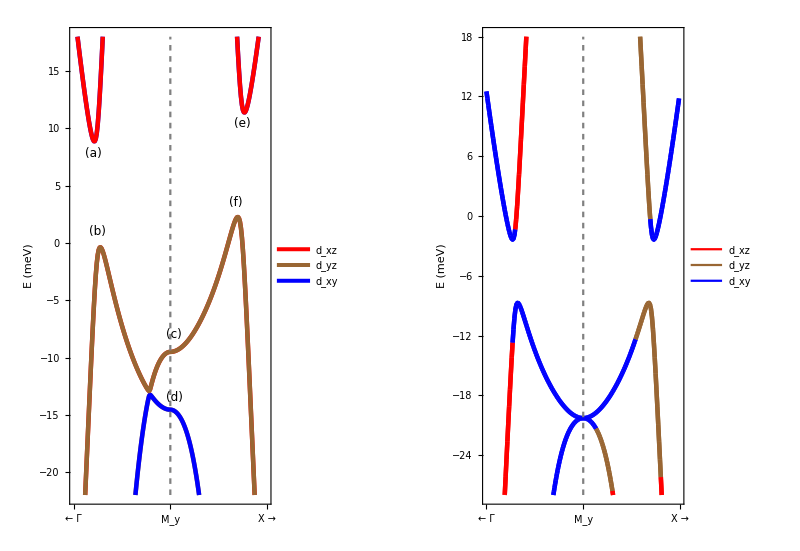

```mathematica
GraphicsRow[{PanelCritPts,PltTemp}]
```

The dominant orbitals seem to have changed. (Note that we have computed the total contribution of each type of orbital across both the Ru atoms and both spin species).

## Phase diagrams

We will now generate the phase diagram for the SOC gap singularities that is included in the manuscript

```mathematica
θmin=7;
θmax=12(*9.6*);

cm=72/2.54;

TicsFontSize=6;
AxesFontSize=8;
RegionFontColour=LightGray;
FigLength=3.5cm;
LeftPadding=0.5cm;
RightPadding=0.2cm;
BottomPadding=0.5cm;
TopPadding=0.15cm;
xTicsLabeled={{7,"7"},{8,"8"},{9,"9"},{10,"10"},{11,"11"},{12,"12"}};
xTics={7,8,9,10,11,12};
yTics={0,0.5,1,1.5,2};

VHsColour={((*125*)161)/255,((*9*)93)/255,((*184*)216)/255,1(*0.65*)};
MinColour={((*9*)59)/255,((*73*)96)/255,((*184*)196)/255,1(*0.65*)};
MaxColour={((*207*)242)/255,((*17*)70)/255,((*51*)70)/255,1(*0.65*)};

PanA=ParametricPlot[{{v FitFunc3[u]+θmin(1-v),u},{(1-v)FitFunc3[u]+θmax v,u}},{u,0,2},{v,0,1},PlotRange->{{θmin,θmax},{0,2}},Frame->True,PlotStyle->{RGBColor[VHsColour],RGBColor[MinColour]},AspectRatio->1,(*FrameTicks->{True,True},*)(*FrameLabel->{None,Style["Δ_nem (%)",FontFamily->"Arial",FontSize->AxesFontSize,FontColor->Black]},*)FrameTicksStyle->{Directive[Black,FontFamily->"Arial",TicsFontSize],{Directive[Black,FontOpacity->0,FontSize->0],Directive[Black,FontOpacity->0,FontSize->0]}},FrameTicks->{True,{xTics,xTics}},ImagePadding->{{LeftPadding,RightPadding},{0.6TopPadding,TopPadding}},ImageSize->FigLength];

PanAp2=ParametricPlot[{FitFunc3[u],u},{u,0,4},Axes->False,Frame->False,PlotStyle->{Black,Thickness[0.018]},PlotRange->{{θmin,θmax},{0,2}},PlotLegends->Placed[LineLegend[{Style["A_3",FontFamily->"Arial",FontSize->TicsFontSize,FontColor->RegionFontColour]},LegendMarkerSize->{10,1.3}],{{0.25,0.92},{0.5,0.5}}]];

Labeled[Show[PanA,PanAp2],{Style["Δ_nem (%)",FontFamily->"Arial",FontSize->AxesFontSize,FontColor->Black],""},{Left,Bottom},Spacings->{0, 0},RotateLabel->True]


PanB=ParametricPlot[{{v FitFunc4[u]+θmin(1-v),u},{(1-v)FitFunc4[u]+θmax v,u}},{u,0,2},{v,0,1},PlotRange->{{θmin,θmax},{0,2}},Frame->True,PlotStyle->{RGBColor[MaxColour],RGBColor[VHsColour]},AspectRatio->1,FrameTicksStyle->{Directive[Black,FontFamily->"Arial",TicsFontSize],{Directive[Black,FontFamily->"Arial",TicsFontSize],Directive[Black,FontOpacity->0,FontSize->0]}},FrameTicks->{True,{xTicsLabeled,xTics}},ImagePadding->{{LeftPadding,RightPadding},{BottomPadding,0.6TopPadding}},ImageSize->FigLength];

PanBp2=ParametricPlot[{FitFunc4[u],u},{u,0,2},Axes->False,Frame->False,PlotStyle->{Black,Thickness[0.018]},PlotLegends->Placed[LineLegend[{Style["A_3",FontFamily->"Arial",FontSize->TicsFontSize,FontColor->RegionFontColour]},LegendMarkerSize->{10,1.3}],{{0.25,0.92},{0.5,0.5}}]];

Labeled[Show[PanB,PanBp2],{Style["Δ_nem (%)",FontFamily->"Arial",FontSize->AxesFontSize,FontColor->Black],Style["θ (°)",FontFamily->"Arial",FontSize->AxesFontSize,FontColor->Black]},{Left,Bottom},Spacings->{0, 0},RotateLabel->True]
```

-Graphics-Δ_nem (%)

-Graphics-Δ_nem (%)θ (°)

```mathematica
PanC=ParametricPlot[{{v FitFunc5[u]+θmin(1-v),u},{(1-v)FitFunc5[u]+θmax v,u}},{u,0,2},{v,0,1},PlotRange->{{θmin,θmax},{0,2}},Frame->True,PlotStyle->{RGBColor[VHsColour],RGBColor[MinColour]},AspectRatio->1,(*FrameTicks->{True,True},*)(*FrameLabel->{None,Style["Δ_nem (%)",FontFamily->"Arial",FontSize->AxesFontSize,FontColor->Black]},*)FrameTicksStyle->{{Directive[Black,FontOpacity->0,FontSize->0],Directive[Black,FontOpacity->0,FontSize->0]},{Directive[Black,FontOpacity->0,FontSize->0],Directive[Black,FontOpacity->0,FontSize->0]}},FrameTicks->{{yTics,yTics},{xTics,xTics}},ImagePadding->{{LeftPadding,RightPadding},{0.6TopPadding,TopPadding}},ImageSize->FigLength];

PanCp2=ParametricPlot[{FitFunc5[u],u},{u,0,4},Axes->False,Frame->False,PlotStyle->{Black,Thickness[0.018]},PlotRange->{{θmin,θmax},{0,2}},PlotLegends->Placed[LineLegend[{Style["A_3",FontFamily->"Arial",FontSize->TicsFontSize,FontColor->RegionFontColour]},LegendMarkerSize->{10,1.3}],{{0.25,0.92},{0.5,0.5}}]];

Show[PanC,PanCp2]
(*Labeled[Show[PanA,PanAp2],{Style["Δ_nem (%)",FontFamily->"Arial",FontSize->AxesFontSize,FontColor->Black],""},{Left,Bottom},Spacings->{0, 0},RotateLabel->True]*)


PanD=ParametricPlot[{{v FitFunc6[u]+θmin(1-v),u},{(1-v)FitFunc6[u]+θmax v,u}},{u,0,2},{v,0,1},PlotRange->{{θmin,θmax},{0,2}},Frame->True,PlotStyle->{RGBColor[VHsColour],RGBColor[MinColour]},AspectRatio->1,FrameTicksStyle->{{Directive[Black,FontOpacity->0,FontSize->0],Directive[Black,FontOpacity->0,FontSize->0]},{Directive[Black,FontFamily->"Arial",TicsFontSize],Directive[Black,FontOpacity->0,FontSize->0]}},FrameTicks->{{yTics,yTics},{xTicsLabeled,xTics}},ImagePadding->{{LeftPadding,RightPadding},{BottomPadding,0.5TopPadding}},ImageSize->FigLength];

PanDp2=ParametricPlot[{FitFunc6[u],u},{u,0,2},Axes->False,Frame->False,PlotStyle->{Black,Thickness[0.018]},PlotLegends->Placed[LineLegend[{Style["A_3",FontFamily->"Arial",FontSize->TicsFontSize,FontColor->RegionFontColour]},LegendMarkerSize->{10,1.3}],{{0.25,0.92},{0.5,0.5}}]];

Show[PanD,PanDp2]
```

-Graphics-

-Graphics-

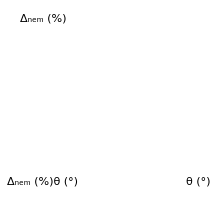

```mathematica
PhaseDiagramFinal=GraphicsGrid[{{Labeled[Show[PanA,PanAp2,Graphics[Rotate[Text[Style["Saddle",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->TicsFontSize],{8,1}],90Degree]],Graphics[Text[Style["Minimum",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->TicsFontSize],{10.5,1.0}]],ListPlot[{{9,0.5}},PlotMarkers->{▲,2.5},PlotStyle->{LightGray,Thickness[0.02]}],Graphics[Text[Style["QPI",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->(TicsFontSize-1)],{9.45,0.5}]],ListPlot[{{8,0.1}},PlotMarkers->{"↓",8},PlotStyle->{LightGray}],Graphics[Text[Style["ARPES",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->(TicsFontSize-1)],{7.9,0.25}]]],{Style["Δ_nem (%)",FontFamily->"Arial",FontSize->AxesFontSize,FontColor->Black]},{Left},Spacings->{0.1, 0},RotateLabel->True,ImageSize->FigLength]
,
Labeled[Show[PanC,PanCp2,Graphics[Rotate[Text[Style["Saddle",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->TicsFontSize],{8,1}],0Degree]],Graphics[Rotate[Text[Style["Minimum",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->TicsFontSize],{11.2,1.0}],90Degree]],ListPlot[{{9,0.5}},PlotMarkers->{▲,2.5},PlotStyle->{LightGray,Thickness[0.02]}],Graphics[Text[Style["QPI",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->(TicsFontSize-1)],{9.45,0.5}]],ListPlot[{{8,0.1}},PlotMarkers->{"↓",8},PlotStyle->{LightGray}],Graphics[Text[Style["ARPES",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->(TicsFontSize-1)],{7.9,0.25}]],ImageSize->FigLength],{Style["",FontSize->0]},{Right},Spacings->{0.1, 0},RotateLabel->True]
},{Labeled[Show[PanB,PanBp2,Graphics[Rotate[Text[Style["Maximum",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->TicsFontSize],{8,1}],90Degree]],Graphics[Text[Style["Saddle",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->TicsFontSize],{10.5,1.0}]],ListPlot[{{9,0.5}},PlotMarkers->{▲,2.5},PlotStyle->{LightGray,Thickness[0.02]}],Graphics[Text[Style["QPI",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->(TicsFontSize-1)],{9.45,0.5}]],ListPlot[{{8,0.1}},PlotMarkers->{"↓",8},PlotStyle->{LightGray}],Graphics[Text[Style["ARPES",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->(TicsFontSize-1)],{7.9,0.25}]]],{Style["Δ_nem (%)",FontFamily->"Arial",FontSize->AxesFontSize,FontColor->Black],Style["θ (°)",FontFamily->"Arial",FontSize->AxesFontSize,FontColor->Black]},{Left,Bottom},Spacings->{0.1, 0},RotateLabel->True],
Labeled[Show[PanD,PanDp2,Graphics[Rotate[Text[Style["Saddle",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->TicsFontSize],{8,1}],0Degree]],Graphics[Rotate[Text[Style["Minimum",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->TicsFontSize],{11.2,1.0}],90Degree]],ListPlot[{{9,0.5}},PlotMarkers->{▲,2.5},PlotStyle->{LightGray,Thickness[0.02]}],Graphics[Text[Style["QPI",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->(TicsFontSize-1)],{9.45,0.5}]],ListPlot[{{8,0.1}},PlotMarkers->{"↓",8},PlotStyle->{LightGray}],Graphics[Text[Style["ARPES",FontFamily->"Arial",FontColor->RegionFontColour,FontSize->(TicsFontSize-1)],{7.9,0.25}]]],{Style["θ (°)",FontFamily->"Arial",FontSize->AxesFontSize,FontColor->Black],Style["",FontSize->0]},{Bottom,Right},Spacings->{0.1, 0},RotateLabel->{True,True}]}},Spacings->{0,-8}]

(*Export[NotebookDirectory[]<>"Phase_horiz.pdf",Show[PhaseDiagramFinal,ImageSize->4.5cm]]*)
```